```mathematica
F[x_]:=1/2 ⅈ (PolyLog[2,-ⅈ ⅇ^x]-PolyLog[2,ⅈ ⅇ^x])
```

```mathematica
G3[a_,b_]:=F[a-b]+F[b-a]-π/2(a+b);
```

```mathematica
EnergySetup[n_,FacesCW_]:=Module[{i,rhoV,rhoF,include,LineFaces,f,Faces,NM,nonlinefaces,radii,RADII},
Faces=Sort/@FacesCW;
f=Length[Faces];
LineFaces={};rhoV=Table[Subscript[rV, i],{i,1,n-2}];rhoF=Table[Subscript[rF, i],{i,1,f-2}];
include = {};
nonlinefaces={};
For[i=1,i≤f,i++,
If[!(Faces[[i,-2]]==n-1&&Faces[[i,-1]]==n),
(* then *) AppendTo[include,i];AppendTo[nonlinefaces,FacesCW[[i]]],
(* else *) AppendTo[LineFaces,i]]];

NM=NMinimize[{∑_(k=1)^(f-2) ∑_(i=1)^Length[Faces[[include[[k]]]]] If[Faces[[include[[k]],i]]<n-1,G3[Subscript[rV, Faces[[include[[k]],i]]],Subscript[rF, k]],0]+∑_(i=1)^(n-2) Subscript[rV, i] π If[MemberQ[Flatten@Table[Faces[[LineFaces[[m]]]],{m,1,2}],i],(* then *) 1,(* else *) 2]+∑_(j=1)^(f-2) Subscript[rF, j] π If[MemberQ[Faces[[include[[j]]]],n-1]||MemberQ[Faces[[include[[j]]]],n],(* then *) 1,(* else *) 2],
∑_(i=1)^(n-2) Subscript[rV, i]+∑_(j=1)^(f-2) Subscript[rF, j]==0},Join[rhoV,rhoF]];
RADII=Exp[Re[Join[rhoV,rhoF]/.(NM[[2]])]];
RADII/=RADII[[1]];
radii=<||>;
For[i=1,i≤n-2,i++,
radii[i]=RADII[[i]]
];
For[i=1,i≤Length[nonlinefaces],i++,
radii[nonlinefaces[[i]]]=RADII[[n-2+i]]
];
{radii,LineFaces}
];
```

```mathematica
Boundary[n_,FacesCW_,LineFaces_,radii_,ϵ_:0]:=Module[{i,j,faces,vertices,lastvisited,d,h,H,breaker,unvisited,f,endcircle,ComputeEndcircle,ComputeEndcircle2,delete},
unvisited =FacesCW;(*Keeps track of the faces we haven't visited*)
f=Length[FacesCW];

faces=<||>; (* centers of face circles (or normals, for lines) *)
For[i=1,i≤f,i++,faces[FacesCW[[i]]]={-∞,-∞}];
vertices=<||>; (* centers of vertex circles (or normals, for lines) *)
For[i=1,i≤n-2,i++,vertices[i]={-∞,-∞}];
(* Radii is an assoc from v->rad and facelist->rad *)

(*Vertex circles going vertically upwards along first FaceLine*)
h=0; (* height along the left line *)
For[i=1,i≤Length[FacesCW[[LineFaces[[1]]]]]-2(*Number of vertex circles that lie along first LineFace*),i++,
vertices[FacesCW[[LineFaces[[1]],i]]]={0,h+radii[FacesCW[[LineFaces[[1]],i]]]};(*Set the center of this vertex circle*)
h+=2radii[[FacesCW[[LineFaces[[1]],i]]]]];(*Keeps track of our cumulative height as we climb up the first FaceLine*)

unvisited=Delete[unvisited,Position[unvisited,FacesCW[[LineFaces[[1]]]]]];

d=0;(*Horizontal distance*)

ComputeEndcircle[prev_,face_]:=
(*Returns which vertex circle we calculated last based on previous vertex circle and face*)
If[face[[Mod[Position[face,n-1][[1,1]]-2,Length[face]]+1]]==prev,
(*then*)face[[Mod[Position[face,n-1][[1,1]],Length[face]]+1]],
(*else*) face[[Mod[Position[face,n-1][[1,1]]-2,Length[face]]+1]]];

endcircle=ComputeEndcircle[n,FacesCW[[LineFaces[[1]]]]];(*Previous vertex circle is bottom line, face is first FaceLine*)

(*Face circles going horizontally across upper vertex line*)
breaker=True;
For[j=1,j≤f ,j++,
For[i=1,i≤Length[unvisited],i++,
If[MemberQ[unvisited[[i]],n-1], (*determine if this face-circle contains n-1, so it is on the upper vertex line*)
If[MemberQ[unvisited[[i]],ComputeEndcircle[endcircle,unvisited[[i]]]],
(*determine if this face-circle also contains the vertex right before n-1 to ensure we are going horizontally across in the right order*)
If[unvisited[[i]]==FacesCW[[LineFaces[[2]]]],
(* If we've reached the second faceline, then do nothing--find the other face circle containing endcircle*)
,
(* else if the face circle is not a line*)
faces[unvisited[[i]]]={d+radii[unvisited[[i]]],h}; (*Set the center of this face circle*)
d+=2radii[unvisited[[i]]]; (* update how far along the top line we are *)
endcircle=ComputeEndcircle[endcircle,unvisited[[i]]];(*Update endcircle*)
unvisited=Delete[unvisited,i];] (* remove that face from the unvisited list *)
]
]
]
];
(*Vertex circles along the second FaceLine, climbing vertically upwards*)
h=0;
For[i=1,i≤Length[FacesCW[[LineFaces[[2]]]]]-2,i++,
vertices[FacesCW[[LineFaces[[2]],i]]]={d,h+radii[FacesCW[[LineFaces[[2]],i]]]};h+=2radii[[FacesCW[[LineFaces[[2]],i]]]]];
H=h;
h=0;(*Reset height*)

ComputeEndcircle2[prev_,face_]:=
If[face[[Mod[Position[face,n][[1,1]]-2,Length[face]]+1]]==prev,
(*then*)face[[Mod[Position[face,n][[1,1]],Length[face]]+1]],
(*else*) face[[Mod[Position[face,n][[1,1]]-2,Length[face]]+1]]];

endcircle=ComputeEndcircle2[n-1,FacesCW[[LineFaces[[1]]]]];
(*Face circles along lower vertex line, moving horizontally from origin to second FaceLine*)
d=0;(*Reset distance*)
breaker=True;
For[j=1,j≤f,j++,
For[i=1,i≤Length[unvisited],i++,
If[MemberQ[unvisited[[i]],n], (* determine if this face-circle contains n *)
If[MemberQ[unvisited[[i]],endcircle(* ComputeEndcircle2[endcircle,unvisited[[i]]] *)],(* determine if this face-cirlce also contains the vertex right before n *)
If[unvisited[[i]]==FacesCW[[LineFaces[[2]]]],
(* If we've reached the second faceline, then do nothing*)
,
(* else *)
faces[unvisited[[i]]]={d+radii[unvisited[[i]]],h}; (* then we'll make this face's center be where we know it is *)
d+=2radii[unvisited[[i]]]; (* update how far along the bottom line we are *)
endcircle=ComputeEndcircle2[endcircle,unvisited[[i]]];
unvisited=Delete[unvisited,i];] (* remove that face from the unvisited list *)
]
]
]
];
(*Set the normals of the vertex lines and face lines*)
faces[FacesCW[[LineFaces[[2]]]]]={1,0};
faces[FacesCW[[LineFaces[[1]]]]]={-1,0};
vertices[n]={0,-1};
vertices[n-1]={0,1};

If[ThrowOrderError[faces,vertices,radii,d,H,n,FacesCW[[LineFaces]],0],
faces[FacesCW[[LineFaces[[1]]]]]*=-1;
faces[FacesCW[[LineFaces[[2]]]]]*=-1;
For[i=1,i≤n,i++,
If[i==n-1||i==n,
,
If[Abs[vertices[i][[1]]-d]≤ϵ,
vertices[i]={0,vertices[i][[2]]},
If[Abs[vertices[i][[1]]-0]≤ϵ,
vertices[i]={d,vertices[i][[2]]}]];
]]];

(*Return the assoc's of the faces to their centers and vertices to their centers*)
{vertices,faces,d,H}
];
```

```mathematica
FindRest[{x_,y_},r_,face_,vertices_,radii_,lines_]:=(* face is all the vertices that the face intersects *)
(*{x_,y_},r: known center of opposite kind and its radius
face: all the circles of its kind that pass thru that opposite known circle
vertices: all the circles of its kind that are tangent to the one we'e looking for*)
Module[{verts=vertices,i,j,ϕ,θ,ω,face2=face,b,b2=True},

If[verts[face2[[1]]]=={-∞,-∞}||MemberQ[lines,face2[[1]]],
For[i=2,i≤Length[face2]&&b2,i++,
If[verts[face2[[i]]]≠{-∞,-∞}&&!MemberQ[lines,face2[[i]]],
face2=Join[face2[[i;;]],face2[[;;i-1]]];
b2=False;
]]];

b=True;
For[i=2,i≤Length[face2]&&b,i++,
If[MemberQ[lines,face2[[i]]],
AppendTo[face2,face2[[1]]];
For[j=Length[face2]-1,j>i,j--,
If[verts[face2[[j]]]=={-∞,-∞},
ϕ=ArcTan[verts[face2[[j+1]]][[1]]-x,verts[face2[[j+1]]][[2]]-y];
θ=ArcTan[radii[face2[[j+1]]]/r];(* j+1 refers to previously computed / known *)
ω=ArcTan[radii[face2[[j]]]/r];
verts[face2[[j]]]={x+√(r^2+radii[face2[[j]]]^2)Cos[ϕ-θ-ω],y+√(r^2+radii[face2[[j]]]^2)Sin[ϕ-θ-ω]}
]
];b=False;Break,
If[verts[face2[[i]]]=={-∞,-∞},
ϕ=ArcTan[verts[face2[[i-1]]][[1]]-x,verts[face2[[i-1]]][[2]]-y];
θ=ArcTan[radii[face2[[i-1]]]/r];(* i-1 refers to previously computed / known *)
ω=ArcTan[radii[face2[[i]]]/r];
verts[face2[[i]]]={x+√(r^2+radii[face2[[i]]]^2)Cos[ϕ+θ+ω],y+√(r^2+radii[face2[[i]]]^2)Sin[ϕ+θ+ω]}];
];];
verts
];
```

```mathematica
Cull[assoc_]:=Module[{vis={},unv={},i},For[i=1,i≤Length[Keys[assoc]],i++,If[assoc[Keys[assoc][[i]]]=={-∞,-∞},AppendTo[unv,Keys[assoc][[i]]],AppendTo[vis,Keys[assoc][[i]]]]];{vis,unv}]
```

```mathematica
Interior[n_,FacesCW_,LineFaces_,radii_,vertices_,faces_,d_,h_]:=
Module[{Vunv={},Funv={},Vvis={},Fvis={},i,j,f,verts=vertices,verts2,fcs=faces,fcs2,fi,vi,x,y,k,b},
f=Length[FacesCW];
For[i=1,i≤n,i++,
If[vertices[i]=={-∞,-∞},AppendTo[Vunv,i],AppendTo[Vvis,i]]];
For[i=1,i≤f,i++,
If[faces[FacesCW[[i]]]=={-∞,-∞},AppendTo[Funv,FacesCW[[i]]],AppendTo[Fvis,FacesCW[[i]]]]];

For[j=1,j≤n+Length[FacesCW]&&(Length[Vunv]+Length[Funv]>0),j++,

For[i=1,i≤Length[Fvis],i++,(* for a known face circle *)
If[Length[Intersection[Vvis,Fvis[[i]]]]*Length[Intersection[Vunv,Fvis[[i]]]]>0,
fi=Fvis[[i]];
{x,y}=fcs[fi];
verts2=FindRest[{x,y},radii[fi],fi,verts,radii,{n-1,n}];
If[ThrowOrderError[fcs,verts2,radii,d,h,n,{FacesCW[[LineFaces[[1]]]],FacesCW[[LineFaces[[2]]]]},0],verts=FindRest[{x,y},radii[fi],Reverse[fi],verts,radii,{n-1,n}],
verts=verts2];
];
{Vvis,Vunv}=Cull[verts];
];

For[i=1,i≤Length[Vvis],i++, (* for a known vertex circle *)
If[b=False;
For[k=1,k≤Length[Fvis],k++,b=b||If[MemberQ[Fvis[[k]],Vvis[[i]]],True,False]];b,
If[b=False;For[k=1,k≤Length[Funv],k++,b=b||If[MemberQ[Funv[[k]],Vvis[[i]]],True,False]];b,
(* then *)
vi=Vvis[[i]];
{x,y}=verts[vi];
fcs2=FindRest[{x,y},radii[vi],FacesList[vi,FacesCW],fcs,radii,FacesCW[[LineFaces]]];
If[ThrowOrderError[fcs2,verts,radii,d,h,n,FacesCW[[LineFaces]],0],
fcs=FindRest[{x,y},radii[vi],
Reverse[FacesList[vi,FacesCW]],fcs,radii,FacesCW[[LineFaces]]],
fcs=fcs2];
];
{Fvis,Funv}=Cull[fcs];
]
];
];
{verts,fcs}
];
```

```mathematica
ThrowOrderError[fcs2_,verts_,radii_,d_,h_,n_,fls_,ϵ_](* fcs2 is proposed fcs association. fls is facelines *):=
Module[{i,j,b,b2,K},
K={};
For[i=1,i≤Length[Keys[fcs2]],i++,
If[!MemberQ[fls,Keys[fcs2][[i]]],AppendTo[K,Keys[fcs2][[i]]]]
];

b=False; (* "breaker" *)
For[i=1,i≤Length[K]&&!b,i++,
If[b2=False;
-∞<fcs2[K[[i]]][[1]]<0
||-∞<fcs2[K[[i]]][[2]]<0
||fcs2[K[[i]]][[1]]>d
||fcs2[K[[i]]][[2]]>h
||(For[j=1,j≤Length[K[[i]]],j++,
If[K[[i,j]]≠n-1&&K[[i,j]]≠n&&verts[K[[i,j]]]≠{-∞,-∞}&&fcs2[K[[i]]]≠{-∞,-∞},
If[EuclideanDistance[verts[K[[i,j]]],fcs2[K[[i]]]]≥(1-ϵ)(radii[K[[i,j]]]+radii[K[[i]]]),b2=True;Break]]];b2),
b=True,

For[j=1,j≤Length[K]&&!b,j++,
If[i≠j&&fcs2[K[[i]]]≠{-∞,-∞}&&fcs2[K[[j]]]≠{-∞,-∞}&&
EuclideanDistance[fcs2[K[[i]]],fcs2[K[[j]]]]<(1+ϵ)(radii[fcs2[K[[i]]]]+radii[fcs2[K[[j]]]])
,(* then, bad *) b=True]]];
];


For[i=1,i≤Length[fls[[1]]]&&!b,i++,
If[verts[fls[[1,i]]][[1]]≠d/2+fcs2[fls[[1]]][[1]] d/2&&fls[[1,i]]<n-1,b=True]
];
For[i=1,i≤Length[fls[[2]]]&&!b,i++,
If[verts[fls[[2,i]]][[1]]≠d/2+fcs2[fls[[2]]][[1]] d/2&&fls[[2,i]]<n-1,b=True]
];

b
];
```

```mathematica
FacesList[v_,Faces_]:=
Module[{ContainV={},i,L=2,p=3,temp},
For[i=1,i≤Length[Faces],i++,
If[MemberQ[Faces[[i]],v],AppendTo[ContainV,Faces[[i]]]]];
While[L<Length[ContainV],
While[p≤Length[ContainV],
If[Length[Intersection[ContainV[[L-1]],ContainV[[p]]]]==2,
temp=ContainV[[p]];ContainV[[p]]=ContainV[[L]];ContainV[[L]]=temp;p=1+Length[ContainV],
p++]
];
L++;
p=L+1;
];
ContainV];
```

```mathematica
Q=({{0, 1/2, 0, 0}, {1/2, 0, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
```

```mathematica
InvCoords[z_,r_,d_:0]:=If[r==∞,{2d,0,z},{Norm[z]^2/r-r,1/r,z/r}];
```

```mathematica
Gram[SC_]:=SC.Q.Transpose[SC];
SuperCluster[vertices_,faces_,radii_,fls_,d_,h_,n_]:=
Module[{sc={},i},
For[i=1,i≤n-2,i++,AppendTo[sc,Flatten[InvCoords[vertices[i],radii[i]]]]];
AppendTo[sc,Flatten[InvCoords[vertices[n-1],∞,h/2+vertices[n-1][[2]] h/2]]];
AppendTo[sc,Flatten[InvCoords[vertices[n],∞,h/2+vertices[n][[2]] h/2]]];
For[i=1,i≤Length[Keys[faces]],i++,
If[!MemberQ[fls,Keys[faces][[i]]],
AppendTo[sc,Flatten[InvCoords[faces[Keys[faces][[i]]],radii[Keys[faces][[i]]]]]]
]];
AppendTo[sc,Flatten[InvCoords[faces[fls[[1]]],∞,d/2+faces[fls[[1]]][[1]] d/2]]];
AppendTo[sc,Flatten[InvCoords[faces[fls[[2]]],∞,d/2+faces[fls[[2]]][[1]] d/2]]];
sc
];
```

```mathematica
DrawCircle[{bhat_,b_,bx_,by_}]:=If[Abs[b]≥ .01,Circle[{bx,by}/b,1/b],InfiniteLine[{bx,by}bhat/2,{-by,bx}]];
```

```mathematica
Packing[n_,FacesCW_,ϵ_:0]:=
Module[{radii,LineFaces,vertices,faces,d,h},
{radii,LineFaces}=EnergySetup[n,FacesCW];
{vertices,faces,d,h}=Boundary[n,FacesCW,LineFaces,radii,ϵ];
{vertices,faces}=Interior[n,FacesCW,LineFaces,radii,vertices,faces,d,h];
{vertices,faces,radii,d,h,LineFaces}];
```

```mathematica
Render[radii_,fcs_,verts_,fls_,n_,d_,h_]:=Graphics[{Blue,Thick,
Table[If[i==n-1,Line[{{-Max[Values[radii]],h},{d+Max[Values[radii]],h}}],If[i==n,Line[{{-Max[Values[radii]],0},{d+Max[Values[radii]],0}}],
Circle[verts[Keys[verts][[i]]],radii[Keys[verts][[i]]]]]],{i,1,n}],
Red,Dashed,
Table[If[Keys[fcs][[i]]==fls[[1]],Line[{{0,-Max[Values[radii]]},{0,h+Max[Values[radii]]}}],
If[Keys[fcs][[i]]==fls[[2]],Line[{{d,-Max[Values[radii]]},{d,h+Max[Values[radii]]}}],
Circle[fcs[Keys[fcs][[i]]],radii[Keys[fcs][[i]]]]]],{i,1,Length[Keys[fcs]]}]
}];
```

```mathematica
SendToInt[ϵ_:0][y_]:=With[{x=Simplify[y]},If[Abs[x-Floor[x]]≤ϵ ,Floor[x],
If[Abs[x-Ceiling[x]]≤ ϵ ,Ceiling[x],x],x]];
```

```mathematica
R[vhat_]:=IdentityMatrix[4]+2Q.Transpose[{vhat}].{vhat}
BMat[n_]:=Table[b[i,j],{i,1,n},{j,1,n}];

Bend[V_,m_][i_]:=
Module[{sol,assignments,rest,l,others1,others2},
sol=Solve[BMat[m].(V[[;;m]])==(V[[;;m]]).R[V[[m+i]]]][[1]];
assignments=Association[sol];
rest=Complement[Flatten[BMat[m]],Keys[assignments]];
l=Length[rest];
others1=Solve[rest==Table[0,{j,1,l}]][[1]];
others2=<||>;
For[j=1,j≤l,j++,others2[rest[[j]]]=Subscript[a, j]];
others2=Normal[others2];
Column[{
MatrixForm[(BMat[m]/.assignments)/.others2],
MatrixForm[(BMat[m]/.assignments)/.others1]
}]
];
```

```mathematica
Everything[n_,FacesCW_,ϵ_:0,steps_,sizemax_:∞]:=Module[{vertices,faces,f=Length[FacesCW],radii,d,h,LineFaces,Vnye,Vout,bends={}},
{vertices,faces,radii,d,h,LineFaces}=Packing[n,FacesCW,ϵ];
Vnye=SendToInt[ϵ]//@SuperCluster[vertices,faces,radii,FacesCW[[LineFaces]],d,h,n];
Vout=MatrixForm[Simplify[RootApproximant[Vnye]]];
bends=Bend[Vout[[1]],n]/@Range@f;
Column[{
Render[radii,faces,vertices,FacesCW[[LineFaces]],n,d,h],
Graphics[{Thick, DrawCircle/@Orbit[Vnye[[-f;;]],Vnye[[;;n]],steps,sizemax],Red,DrawCircle/@Vnye[[-f;;]], Blue, DrawCircle/@Vnye[[;;n]]},PlotRange->{{-d,2 d},{-1.2 Max[Values[radii]],h+1.2 Max[Values[radii]]}},PlotRangeClipping->True],
Vout,
bends,
MatrixForm[Simplify[RootApproximant[
SendToInt[ϵ]//@Gram[SuperCluster[vertices,faces,radii,FacesCW[[LineFaces]],d,h,n]]]
]]
}]]
```

```mathematica
Orbit[co_,cl_,steps_,sizemax_:∞]:=Module[{i,j,k,orbit=cl,L},
For[i=1,i≤steps,i++,
L=Length[orbit];
For[j=1,j≤Length[co],j++,
For[k=1,k≤L,k++,
If[(orbit⟦k⟧.R[co⟦j⟧])⟦2⟧≤sizemax&&!MemberQ[Round[N[orbit],.001],Round[N[orbit⟦k⟧.R[co⟦j⟧]],.001](*new thing*)],AppendTo[orbit,orbit⟦k⟧.R[co⟦j⟧](*newthing*)]]
]
]
];
orbit
];
```

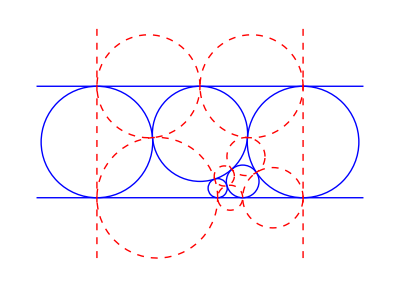
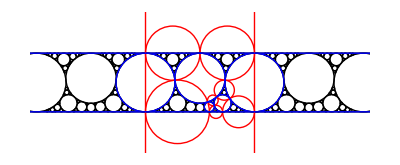
-Graphics-
-Graphics-
(96-64 √2 | 1 | 2 √(4-2 √2) | 7-4 √2
0 | 1/4 (2+√2) | 0 | 1
32 | 1/4 (10+7 √2) | 2/149 (26+√835374) | 1
8 (2+√2) | 3/2+√2 | 2 √(10+7 √2) | 1
16 | 1/4 (2+√2) | 2 √(2+√2) | 1
-8 (-2+√2) | 0 | 0 | 1
0 | 0 | 0 | -1
Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3] | (√(2+√2))/2 | 1 | 2 √(4-2 √2)
Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3] | (√(2+√2))/2 | 3 | 2 √(4-2 √2)
Root[156+113 #1-1823 #1^2+70 #1^3&,3] | √(13/4+17/(4 √2)) | 5+2 √2 | 2 √(4-2 √2)
Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2] | 3/2 √(5+7/(√2)) | 7+4 √2 | 2 √(4-2 √2)
Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4] | √(5/4+7/(4 √2)) | 3+2 √2 | 0
Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2] | √(29/4+41/(4 √2)) | 5+4 √2 | 0
0 | 1/4 √(5+7/(√2)) | 1 | 0
0 | 0 | -1 | 0
Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2] | 0 | 1 | 0)
{(a_1 | -(14304+9536 √2+3328 √(2 (2-√2))+256 √(417687 (2-√2))-3536 √(2+√2)+1664 √(2 (2+√2))+128 √(417687 (2+√2))-136 √(835374 (2+√2))-14900 √((2-√2) (2+√2))-11324 √(2 (2-√2) (2+√2))-208 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-104 √2 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-8 √417687 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-8 √835374 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+1490 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+1043 √(2 (2+√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])/(2 (2+√2)^(3/2) (26+√835374))+(2 (-52-2 √835374+1043 √(2-√2)+745 √(2 (2-√2))) a_1)/((2+√2) (26+√835374))-((156+104 √2+8 √417687+6 √835374-1490 √(10+7 √2)-1043 √(2 (10+7 √2))) a_2)/((2+√2) (26+√835374))-((-1490-1043 √2+26 √(2+√2)+√(835374 (2+√2))) a_3)/(√(2+√2) (26+√835374)) | -(149 (-32 √(2-√2)+30 √(2 (2-√2))-48 √(2+√2)+32 √(2 (2+√2))-Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_1)/(26+√835374)-(149 √(10+7 √2) a_2)/(26+√835374)-(149 √(2+√2) a_3)/(26+√835374) | a_2 | a_3 | -(2496-1664 √2-128 √417687+96 √835374-76288 √(2-√2)+71520 √(2 (2-√2))-114432 √(2+√2)+76288 √(2 (2+√2))-2384 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+832 √(2-√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-832 √(2 (2-√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-64 √(417687 (2-√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+32 √(835374 (2-√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+1248 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-832 √(2 (2+√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-64 √(417687 (2+√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+48 √(835374 (2+√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+26 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2+√835374 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2)/(8 (-2+√2) (26+√835374))-(4 (-78+52 √2+4 √417687-3 √835374+149 √(2 (2-√2))) a_1)/((-2+√2) (26+√835374))+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_2)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_3)/((-2+√2) (26+√835374)) | -(-114432-76288 √2-13312 √(2 (2-√2))-1024 √(417687 (2-√2))+40352 √(2+√2)-19760 √(2 (2+√2))-1520 √(417687 (2+√2))+1552 √(835374 (2+√2))+119200 √((2-√2) (2+√2))+90592 √(2 (2-√2) (2+√2))-1664 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-832 √2 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-64 √417687 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-64 √835374 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-11920 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-8344 √(2 (2+√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+78 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2+52 √(2 (2+√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2+4 √(417687 (2+√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2+3 √(835374 (2+√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2)/(4 (-2+√2) (2+√2)^(5/2) (26+√835374))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_1)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_2)/((-2+√2) (2+√2) (26+√835374))+(2 (-894-596 √2+26 √(2+√2)+√(835374 (2+√2))) a_3)/((-2+√2) √(2+√2) (26+√835374))
a_4 | (149 (10+7 √2) (4 √(4-2 √2)-1/4 (2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(2 (2+√2) (26+√835374))-(4 (2 √((4-2 √2) (2+√2))-1/4 (2+√2) (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])))/(2+√2)-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_4-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_5-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_6 | -(149 (4 √(4-2 √2)-1/4 (2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_4)/(26+√835374)-(149 √(10+7 √2) a_5)/(26+√835374)-(149 √(2+√2) a_6)/(26+√835374) | a_5 | a_6 | -(298 (4 √(4-2 √2)-1/4 (2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-1/4 (2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2)/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_4+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_5)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_6)/((-2+√2) (26+√835374)) | -(298 (3+2 √2) (4 √(4-2 √2)-1/4 (2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/((-2+√2) (2+√2) (26+√835374))-(3008-2016 √2-48 √(2 (2-√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+2 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2+√2 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2)/(32 (-2+√2))-(4 (2 √((4-2 √2) (2+√2))-1/4 (2+√2) (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])))/(2+√2)-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_4)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_5)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_6
a_7 | (149 (10+7 √2) (4 √(4-2 √2)-16 √(2+√2)+2/149 (26+√835374)-1/4 (10+7 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(2 (2+√2) (26+√835374))-(4 (-8 (2+√2)+2 √((4-2 √2) (2+√2))+2/149 √(2+√2) (26+√835374)-1/4 (10+7 √2) (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])))/(2+√2)-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_7-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_8-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_9 | -(149 (4 √(4-2 √2)-16 √(2+√2)+2/149 (26+√835374)-1/4 (10+7 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_7)/(26+√835374)-(149 √(10+7 √2) a_8)/(26+√835374)-(149 √(2+√2) a_9)/(26+√835374) | a_8 | a_9 | -(298 (4 √(4-2 √2)-16 √(2+√2)+2/149 (26+√835374)-1/4 (10+7 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+4/149 (26+√835374) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-1/4 (10+7 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2-32 (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_7+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_8)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_9)/((-2+√2) (26+√835374)) | 1/149 (-4917-2384 √2+208 √(2 (2-√2))+16 √(417687 (2-√2))-1043 √(2-√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-745 √(2 (2-√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])-(298 (3+2 √2) (4 √(4-2 √2)-16 √(2+√2)+2/149 (26+√835374)-1/4 (10+7 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/((-2+√2) (2+√2) (26+√835374))+(4 √(4-2 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+4/149 (26+√835374) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-1/4 (10+7 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2-32 (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(8 (-2+√2))-(4 (-8 (2+√2)+2 √((4-2 √2) (2+√2))+2/149 √(2+√2) (26+√835374)-1/4 (10+7 √2) (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])))/(2+√2)-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_7)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_8)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_9
a_10 | (149 (10+7 √2) (4 √(4-2 √2)-4 (2+√2)^(3/2)+2 √(10+7 √2)-(3/2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(2 (2+√2) (26+√835374))-(4 (-2 (2+√2)^2+2 √((4-2 √2) (2+√2))+2 √((2+√2) (10+7 √2))-(3/2+√2) (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])))/(2+√2)-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_10-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_11-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_12 | -(149 (4 √(4-2 √2)-4 (2+√2)^(3/2)+2 √(10+7 √2)-(3/2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_10)/(26+√835374)-(149 √(10+7 √2) a_11)/(26+√835374)-(149 √(2+√2) a_12)/(26+√835374) | a_11 | a_12 | -(298 (4 √(4-2 √2)-4 (2+√2)^(3/2)+2 √(10+7 √2)-(3/2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+4 √(10+7 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-(3/2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2-8 (2+√2) (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_10+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_11)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_12)/((-2+√2) (26+√835374)) | -(298 (3+2 √2) (4 √(4-2 √2)-4 (2+√2)^(3/2)+2 √(10+7 √2)-(3/2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/((-2+√2) (2+√2) (26+√835374))-(128-416 √2+512 √(3+2 √2)+256 √(17+12 √2)-256 √(2 (17+12 √2))-144 √(2-√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-112 √(2 (2-√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+80 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+48 √(2 (2+√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-16 √(10+7 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-8 √(2 (10+7 √2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+10 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2+7 √2 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2)/(16 (-2+√2) (2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_10)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_11)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_12
a_13 | (149 (10+7 √2) (4 √(4-2 √2)-6 √(2+√2)-1/4 (2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(2 (2+√2) (26+√835374))-(4 (-2 (2+√2)+2 √((4-2 √2) (2+√2))-1/4 (2+√2) (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])))/(2+√2)-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_13-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_14-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_15 | -(149 (4 √(4-2 √2)-6 √(2+√2)-1/4 (2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_13)/(26+√835374)-(149 √(10+7 √2) a_14)/(26+√835374)-(149 √(2+√2) a_15)/(26+√835374) | a_14 | a_15 | -(298 (4 √(4-2 √2)-6 √(2+√2)-1/4 (2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/((-2+√2) (26+√835374))-(64-16 √(2 (2-√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+16 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+2 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2+√2 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2)/(32 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_13+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_14)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_15)/((-2+√2) (26+√835374)) | -(298 (3+2 √2) (4 √(4-2 √2)-6 √(2+√2)-1/4 (2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/((-2+√2) (2+√2) (26+√835374))-(2048-1504 √2-48 √(2 (2-√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+16 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+2 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2+√2 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2)/(32 (-2+√2))-(4 (-2 (2+√2)+2 √((4-2 √2) (2+√2))-1/4 (2+√2) (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])))/(2+√2)-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_13)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_14)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_15
a_16 | -(16 (-1+√((2-√2)/(2+√2))+√((2 (2-√2))/(2+√2))))/(2+√2)+(298 (10+7 √2) (√(2 (2-√2))-2 √(2+√2)+√(2 (2+√2))))/((2+√2) (26+√835374))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_16-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_17-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_18 | -(298 (√(2 (2-√2))-2 √(2+√2)+√(2 (2+√2))))/(26+√835374)-(149 √(2 (2-√2)) a_16)/(26+√835374)-(149 √(10+7 √2) a_17)/(26+√835374)-(149 √(2+√2) a_18)/(26+√835374) | a_17 | a_18 | -(1192 (√(2 (2-√2))-2 √(2+√2)+√(2 (2+√2))))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+8 (-2+√2) (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_16+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_17)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_18)/((-2+√2) (26+√835374)) | -1-(16 (-1+√((2-√2)/(2+√2))+√((2 (2-√2))/(2+√2))))/(2+√2)-(1192 (3+2 √2) (√(2 (2-√2))-2 √(2+√2)+√(2 (2+√2))))/((-2+√2) (2+√2) (26+√835374))+(4 √(4-2 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+8 (-2+√2) (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(8 (-2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_16)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_17)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_18
a_19 | 8 √((2 (2-√2))/(2+√2))-(298 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_19-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_20-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_21 | (298 √(2 (2-√2)))/(26+√835374)-(149 √(2 (2-√2)) a_19)/(26+√835374)-(149 √(10+7 √2) a_20)/(26+√835374)-(149 √(2+√2) a_21)/(26+√835374) | a_20 | a_21 | (1192 √(2 (2-√2)))/((-2+√2) (26+√835374))-(√(1/2 (2-√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])/(-2+√2)-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_19+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_20)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_21)/((-2+√2) (26+√835374)) | 8 √((2 (2-√2))/(2+√2))+(1192 √(2 (2-√2)) (3+2 √2))/((-2+√2) (2+√2) (26+√835374))-(-188+126 √2+√(2 (2-√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])/(2 (-2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_19)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_20)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_21)
(0 | -(14304+9536 √2+3328 √(2 (2-√2))+256 √(417687 (2-√2))-3536 √(2+√2)+1664 √(2 (2+√2))+128 √(417687 (2+√2))-136 √(835374 (2+√2))-14900 √((2-√2) (2+√2))-11324 √(2 (2-√2) (2+√2))-208 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-104 √2 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-8 √417687 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-8 √835374 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+1490 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+1043 √(2 (2+√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])/(2 (2+√2)^(3/2) (26+√835374)) | -(149 (-32 √(2-√2)+30 √(2 (2-√2))-48 √(2+√2)+32 √(2 (2+√2))-Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(2 (26+√835374)) | 0 | 0 | -(2496-1664 √2-128 √417687+96 √835374-76288 √(2-√2)+71520 √(2 (2-√2))-114432 √(2+√2)+76288 √(2 (2+√2))-2384 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+832 √(2-√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-832 √(2 (2-√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-64 √(417687 (2-√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+32 √(835374 (2-√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+1248 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-832 √(2 (2+√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-64 √(417687 (2+√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+48 √(835374 (2+√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+26 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2+√835374 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2)/(8 (-2+√2) (26+√835374)) | -(-114432-76288 √2-13312 √(2 (2-√2))-1024 √(417687 (2-√2))+40352 √(2+√2)-19760 √(2 (2+√2))-1520 √(417687 (2+√2))+1552 √(835374 (2+√2))+119200 √((2-√2) (2+√2))+90592 √(2 (2-√2) (2+√2))-1664 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-832 √2 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-64 √417687 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-64 √835374 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-11920 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-8344 √(2 (2+√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+78 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2+52 √(2 (2+√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2+4 √(417687 (2+√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2+3 √(835374 (2+√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2)/(4 (-2+√2) (2+√2)^(5/2) (26+√835374))
0 | (149 (10+7 √2) (4 √(4-2 √2)-1/4 (2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(2 (2+√2) (26+√835374))-(4 (2 √((4-2 √2) (2+√2))-1/4 (2+√2) (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])))/(2+√2) | -(149 (4 √(4-2 √2)-1/4 (2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(2 (26+√835374)) | 0 | 0 | -(298 (4 √(4-2 √2)-1/4 (2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-1/4 (2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2)/(8 (-2+√2)) | -(298 (3+2 √2) (4 √(4-2 √2)-1/4 (2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/((-2+√2) (2+√2) (26+√835374))-(3008-2016 √2-48 √(2 (2-√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+2 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2+√2 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2)/(32 (-2+√2))-(4 (2 √((4-2 √2) (2+√2))-1/4 (2+√2) (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])))/(2+√2)
0 | (149 (10+7 √2) (4 √(4-2 √2)-16 √(2+√2)+2/149 (26+√835374)-1/4 (10+7 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(2 (2+√2) (26+√835374))-(4 (-8 (2+√2)+2 √((4-2 √2) (2+√2))+2/149 √(2+√2) (26+√835374)-1/4 (10+7 √2) (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])))/(2+√2) | -(149 (4 √(4-2 √2)-16 √(2+√2)+2/149 (26+√835374)-1/4 (10+7 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(2 (26+√835374)) | 0 | 0 | -(298 (4 √(4-2 √2)-16 √(2+√2)+2/149 (26+√835374)-1/4 (10+7 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+4/149 (26+√835374) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-1/4 (10+7 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2-32 (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(8 (-2+√2)) | 1/149 (-4917-2384 √2+208 √(2 (2-√2))+16 √(417687 (2-√2))-1043 √(2-√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-745 √(2 (2-√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])-(298 (3+2 √2) (4 √(4-2 √2)-16 √(2+√2)+2/149 (26+√835374)-1/4 (10+7 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/((-2+√2) (2+√2) (26+√835374))+(4 √(4-2 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+4/149 (26+√835374) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-1/4 (10+7 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2-32 (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(8 (-2+√2))-(4 (-8 (2+√2)+2 √((4-2 √2) (2+√2))+2/149 √(2+√2) (26+√835374)-1/4 (10+7 √2) (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])))/(2+√2)
0 | (149 (10+7 √2) (4 √(4-2 √2)-4 (2+√2)^(3/2)+2 √(10+7 √2)-(3/2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(2 (2+√2) (26+√835374))-(4 (-2 (2+√2)^2+2 √((4-2 √2) (2+√2))+2 √((2+√2) (10+7 √2))-(3/2+√2) (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])))/(2+√2) | -(149 (4 √(4-2 √2)-4 (2+√2)^(3/2)+2 √(10+7 √2)-(3/2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(2 (26+√835374)) | 0 | 0 | -(298 (4 √(4-2 √2)-4 (2+√2)^(3/2)+2 √(10+7 √2)-(3/2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+4 √(10+7 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-(3/2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2-8 (2+√2) (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(8 (-2+√2)) | -(298 (3+2 √2) (4 √(4-2 √2)-4 (2+√2)^(3/2)+2 √(10+7 √2)-(3/2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/((-2+√2) (2+√2) (26+√835374))-(128-416 √2+512 √(3+2 √2)+256 √(17+12 √2)-256 √(2 (17+12 √2))-144 √(2-√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-112 √(2 (2-√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+80 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+48 √(2 (2+√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-16 √(10+7 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]-8 √(2 (10+7 √2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+10 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2+7 √2 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2)/(16 (-2+√2) (2+√2))
0 | (149 (10+7 √2) (4 √(4-2 √2)-6 √(2+√2)-1/4 (2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(2 (2+√2) (26+√835374))-(4 (-2 (2+√2)+2 √((4-2 √2) (2+√2))-1/4 (2+√2) (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])))/(2+√2) | -(149 (4 √(4-2 √2)-6 √(2+√2)-1/4 (2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(2 (26+√835374)) | 0 | 0 | -(298 (4 √(4-2 √2)-6 √(2+√2)-1/4 (2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/((-2+√2) (26+√835374))-(64-16 √(2 (2-√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+16 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+2 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2+√2 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2)/(32 (-2+√2)) | -(298 (3+2 √2) (4 √(4-2 √2)-6 √(2+√2)-1/4 (2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/((-2+√2) (2+√2) (26+√835374))-(2048-1504 √2-48 √(2 (2-√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+16 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+2 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2+√2 Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]^2)/(32 (-2+√2))-(4 (-2 (2+√2)+2 √((4-2 √2) (2+√2))-1/4 (2+√2) (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])))/(2+√2)
0 | -(16 (-1+√((2-√2)/(2+√2))+√((2 (2-√2))/(2+√2))))/(2+√2)+(298 (10+7 √2) (√(2 (2-√2))-2 √(2+√2)+√(2 (2+√2))))/((2+√2) (26+√835374)) | -(298 (√(2 (2-√2))-2 √(2+√2)+√(2 (2+√2))))/(26+√835374) | 0 | 0 | -(1192 (√(2 (2-√2))-2 √(2+√2)+√(2 (2+√2))))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+8 (-2+√2) (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(8 (-2+√2)) | -1-(16 (-1+√((2-√2)/(2+√2))+√((2 (2-√2))/(2+√2))))/(2+√2)-(1192 (3+2 √2) (√(2 (2-√2))-2 √(2+√2)+√(2 (2+√2))))/((-2+√2) (2+√2) (26+√835374))+(4 √(4-2 √2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]+8 (-2+√2) (1+1/2 √(2+√2) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3]))/(8 (-2+√2))
0 | 8 √((2 (2-√2))/(2+√2))-(298 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374)) | (298 √(2 (2-√2)))/(26+√835374) | 0 | 0 | (1192 √(2 (2-√2)))/((-2+√2) (26+√835374))-(√(1/2 (2-√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])/(-2+√2) | 8 √((2 (2-√2))/(2+√2))+(1192 √(2 (2-√2)) (3+2 √2))/((-2+√2) (2+√2) (26+√835374))-(-188+126 √2+√(2 (2-√2)) Root[-1-#1-7 #1^2+#1^4+2 #1^5+9 #1^8+8 #1^9-7 #1^10+#1^11&,3])/(2 (-2+√2))),(a_1 | -(71520+50064 √2+6656 √(2-√2)+5824 √(2 (2-√2))+448 √(417687 (2-√2))+256 √(835374 (2-√2))-1872 √(2+√2)-104 √(2 (2+√2))-8 √(417687 (2+√2))-72 √(835374 (2+√2))-178800 √((2-√2) (2+√2))-127246 √(2 (2-√2) (2+√2))-312 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-208 √2 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-16 √417687 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-12 √835374 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+7599 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+5364 √(2 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3])/((2+√2)^(5/2) (26+√835374))+(2 (-52-2 √835374+1043 √(2-√2)+745 √(2 (2-√2))) a_1)/((2+√2) (26+√835374))-((156+104 √2+8 √417687+6 √835374-1490 √(10+7 √2)-1043 √(2 (10+7 √2))) a_2)/((2+√2) (26+√835374))-((-1490-1043 √2+26 √(2+√2)+√(835374 (2+√2))) a_3)/(√(2+√2) (26+√835374)) | -(149 (-96 √(2-√2)+118 √(2 (2-√2))-144 √(2+√2)+96 √(2 (2+√2))-3 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_1)/(26+√835374)-(149 √(10+7 √2) a_2)/(26+√835374)-(149 √(2+√2) a_3)/(26+√835374) | a_2 | a_3 | -(2496-1664 √2-128 √417687+96 √835374-228864 √(2-√2)+281312 √(2 (2-√2))-343296 √(2+√2)+228864 √(2 (2+√2))-7152 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+832 √(2-√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-1040 √(2 (2-√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-80 √(417687 (2-√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+32 √(835374 (2-√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+1248 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-832 √(2 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-64 √(417687 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+48 √(835374 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+26 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2+√835374 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2)/(8 (-2+√2) (26+√835374))-(4 (-78+52 √2+4 √417687-3 √835374+149 √(2 (2-√2))) a_1)/((-2+√2) (26+√835374))+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_2)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_3)/((-2+√2) (26+√835374)) | -(-343296-228864 √2-6656 √(2-√2)-19968 √(2 (2-√2))-1536 √(417687 (2-√2))-256 √(835374 (2-√2))+53664 √(2+√2)-19760 √(2 (2+√2))-1520 √(417687 (2+√2))+2064 √(835374 (2+√2))+824864 √((2-√2) (2+√2))+605536 √(2 (2-√2) (2+√2))-2912 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-1664 √2 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-128 √417687 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-112 √835374 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-35760 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-25032 √(2 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+78 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2+52 √(2 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2+4 √(417687 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2+3 √(835374 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2)/(4 (-2+√2) (2+√2)^(5/2) (26+√835374))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_1)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_2)/((-2+√2) (2+√2) (26+√835374))+(2 (-894-596 √2+26 √(2+√2)+√(835374 (2+√2))) a_3)/((-2+√2) √(2+√2) (26+√835374))
a_4 | (149 (10+7 √2) (12 √(4-2 √2)-3/4 (2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(2 (2+√2) (26+√835374))-(4 (2 √((4-2 √2) (2+√2))-1/4 (2+√2) (1+1/2 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3])))/(2+√2)-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_4-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_5-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_6 | -(149 (12 √(4-2 √2)-3/4 (2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_4)/(26+√835374)-(149 √(10+7 √2) a_5)/(26+√835374)-(149 √(2+√2) a_6)/(26+√835374) | a_5 | a_6 | -(298 (12 √(4-2 √2)-3/4 (2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-1/4 (2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2)/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_4+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_5)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_6)/((-2+√2) (26+√835374)) | -(298 (3+2 √2) (12 √(4-2 √2)-3/4 (2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/((-2+√2) (2+√2) (26+√835374))-(512-256 √2-48 √(2-√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-48 √(2 (2-√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+16 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+3 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2+2 √2 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2)/(16 (-2+√2) (2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_4)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_5)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_6
a_7 | -(-17284-11622 √2+1248 √(2+√2)+48 √(835374 (2+√2))-1490 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-1043 √(2 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3])/(298 (2+√2))+(149 (10+7 √2) (12 √(4-2 √2)-48 √(2+√2)+34/149 (26+√835374)-3/4 (10+7 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(2 (2+√2) (26+√835374))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_7-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_8-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_9 | -(149 (12 √(4-2 √2)-48 √(2+√2)+34/149 (26+√835374)-3/4 (10+7 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_7)/(26+√835374)-(149 √(10+7 √2) a_8)/(26+√835374)-(149 √(2+√2) a_9)/(26+√835374) | a_8 | a_9 | -(298 (12 √(4-2 √2)-48 √(2+√2)+34/149 (26+√835374)-3/4 (10+7 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+12/149 (26+√835374) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-1/4 (10+7 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2-32 (1+1/2 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_7+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_8)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_9)/((-2+√2) (26+√835374)) | 1/149 (-4917-2384 √2+624 √(2 (2-√2))+48 √(417687 (2-√2))-1043 √(2-√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-745 √(2 (2-√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3])-(-17284-11622 √2+1248 √(2+√2)+48 √(835374 (2+√2))-1490 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-1043 √(2 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3])/(298 (2+√2))-(298 (3+2 √2) (12 √(4-2 √2)-48 √(2+√2)+34/149 (26+√835374)-3/4 (10+7 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/((-2+√2) (2+√2) (26+√835374))+(4 √(4-2 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+12/149 (26+√835374) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-1/4 (10+7 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2-32 (1+1/2 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(8 (-2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_7)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_8)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_9
a_10 | (149 (10+7 √2) (12 √(4-2 √2)-12 (2+√2)^(3/2)+34 √(10+7 √2)-3 (3/2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(2 (2+√2) (26+√835374))-(-38-36 √2+24 √(2 (17+12 √2))-3 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-2 √(2 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3])/(2+√2)-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_10-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_11-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_12 | -(149 (12 √(4-2 √2)-12 (2+√2)^(3/2)+34 √(10+7 √2)-3 (3/2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_10)/(26+√835374)-(149 √(10+7 √2) a_11)/(26+√835374)-(149 √(2+√2) a_12)/(26+√835374) | a_11 | a_12 | -(298 (12 √(4-2 √2)-12 (2+√2)^(3/2)+34 √(10+7 √2)-3 (3/2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+12 √(10+7 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-(3/2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2-8 (2+√2) (1+1/2 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_10+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_11)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_12)/((-2+√2) (26+√835374)) | -(298 (3+2 √2) (12 √(4-2 √2)-12 (2+√2)^(3/2)+34 √(10+7 √2)-3 (3/2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/((-2+√2) (2+√2) (26+√835374))-(128-416 √2+1536 √(3+2 √2)+768 √(17+12 √2)-768 √(2 (17+12 √2))-144 √(2-√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-112 √(2 (2-√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+80 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+48 √(2 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-48 √(10+7 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-24 √(2 (10+7 √2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+10 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2+7 √2 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2)/(16 (-2+√2) (2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_10)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_11)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_12
a_13 | (149 (10+7 √2) (12 √(4-2 √2)+10 √(2+√2)-3/4 (2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(2 (2+√2) (26+√835374))-(60+14 √2-2 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-√(2 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3])/(2 (2+√2))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_13-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_14-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_15 | -(149 (12 √(4-2 √2)+10 √(2+√2)-3/4 (2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_13)/(26+√835374)-(149 √(10+7 √2) a_14)/(26+√835374)-(149 √(2+√2) a_15)/(26+√835374) | a_14 | a_15 | -(298 (12 √(4-2 √2)+10 √(2+√2)-3/4 (2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/((-2+√2) (26+√835374))-(64-16 √(2 (2-√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-16 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+2 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2+√2 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2)/(32 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_13+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_14)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_15)/((-2+√2) (26+√835374)) | -(298 (3+2 √2) (12 √(4-2 √2)+10 √(2+√2)-3/4 (2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/((-2+√2) (2+√2) (26+√835374))-(832-224 √2-48 √(2-√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-48 √(2 (2-√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-8 √(2 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+3 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2+2 √2 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2)/(16 (-2+√2) (2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_13)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_14)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_15
a_16 | -(16 (-1+√((2-√2)/(2+√2))+√((2 (2-√2))/(2+√2))))/(2+√2)+(894 (10+7 √2) (√(2 (2-√2))-2 √(2+√2)+√(2 (2+√2))))/((2+√2) (26+√835374))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_16-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_17-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_18 | -(894 (√(2 (2-√2))-2 √(2+√2)+√(2 (2+√2))))/(26+√835374)-(149 √(2 (2-√2)) a_16)/(26+√835374)-(149 √(10+7 √2) a_17)/(26+√835374)-(149 √(2+√2) a_18)/(26+√835374) | a_17 | a_18 | -(3576 (√(2 (2-√2))-2 √(2+√2)+√(2 (2+√2))))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+8 (-2+√2) (1+1/2 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_16+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_17)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_18)/((-2+√2) (26+√835374)) | -1-(16 (-1+√((2-√2)/(2+√2))+√((2 (2-√2))/(2+√2))))/(2+√2)-(3576 (3+2 √2) (√(2 (2-√2))-2 √(2+√2)+√(2 (2+√2))))/((-2+√2) (2+√2) (26+√835374))+(4 √(4-2 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+8 (-2+√2) (1+1/2 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(8 (-2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_16)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_17)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_18
a_19 | 8 √((2 (2-√2))/(2+√2))-(894 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_19-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_20-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_21 | (894 √(2 (2-√2)))/(26+√835374)-(149 √(2 (2-√2)) a_19)/(26+√835374)-(149 √(10+7 √2) a_20)/(26+√835374)-(149 √(2+√2) a_21)/(26+√835374) | a_20 | a_21 | (3576 √(2 (2-√2)))/((-2+√2) (26+√835374))-(√(1/2 (2-√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3])/(-2+√2)-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_19+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_20)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_21)/((-2+√2) (26+√835374)) | 8 √((2 (2-√2))/(2+√2))+(3576 √(2 (2-√2)) (3+2 √2))/((-2+√2) (2+√2) (26+√835374))-(-188+126 √2+√(2 (2-√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3])/(2 (-2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_19)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_20)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_21)
(0 | -(71520+50064 √2+6656 √(2-√2)+5824 √(2 (2-√2))+448 √(417687 (2-√2))+256 √(835374 (2-√2))-1872 √(2+√2)-104 √(2 (2+√2))-8 √(417687 (2+√2))-72 √(835374 (2+√2))-178800 √((2-√2) (2+√2))-127246 √(2 (2-√2) (2+√2))-312 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-208 √2 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-16 √417687 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-12 √835374 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+7599 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+5364 √(2 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3])/((2+√2)^(5/2) (26+√835374)) | -(149 (-96 √(2-√2)+118 √(2 (2-√2))-144 √(2+√2)+96 √(2 (2+√2))-3 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(2 (26+√835374)) | 0 | 0 | -(2496-1664 √2-128 √417687+96 √835374-228864 √(2-√2)+281312 √(2 (2-√2))-343296 √(2+√2)+228864 √(2 (2+√2))-7152 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+832 √(2-√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-1040 √(2 (2-√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-80 √(417687 (2-√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+32 √(835374 (2-√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+1248 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-832 √(2 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-64 √(417687 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+48 √(835374 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+26 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2+√835374 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2)/(8 (-2+√2) (26+√835374)) | -(-343296-228864 √2-6656 √(2-√2)-19968 √(2 (2-√2))-1536 √(417687 (2-√2))-256 √(835374 (2-√2))+53664 √(2+√2)-19760 √(2 (2+√2))-1520 √(417687 (2+√2))+2064 √(835374 (2+√2))+824864 √((2-√2) (2+√2))+605536 √(2 (2-√2) (2+√2))-2912 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-1664 √2 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-128 √417687 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-112 √835374 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-35760 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-25032 √(2 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+78 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2+52 √(2 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2+4 √(417687 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2+3 √(835374 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2)/(4 (-2+√2) (2+√2)^(5/2) (26+√835374))
0 | (149 (10+7 √2) (12 √(4-2 √2)-3/4 (2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(2 (2+√2) (26+√835374))-(4 (2 √((4-2 √2) (2+√2))-1/4 (2+√2) (1+1/2 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3])))/(2+√2) | -(149 (12 √(4-2 √2)-3/4 (2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(2 (26+√835374)) | 0 | 0 | -(298 (12 √(4-2 √2)-3/4 (2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-1/4 (2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2)/(8 (-2+√2)) | -(298 (3+2 √2) (12 √(4-2 √2)-3/4 (2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/((-2+√2) (2+√2) (26+√835374))-(512-256 √2-48 √(2-√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-48 √(2 (2-√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+16 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+3 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2+2 √2 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2)/(16 (-2+√2) (2+√2))
0 | -(-17284-11622 √2+1248 √(2+√2)+48 √(835374 (2+√2))-1490 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-1043 √(2 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3])/(298 (2+√2))+(149 (10+7 √2) (12 √(4-2 √2)-48 √(2+√2)+34/149 (26+√835374)-3/4 (10+7 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(2 (2+√2) (26+√835374)) | -(149 (12 √(4-2 √2)-48 √(2+√2)+34/149 (26+√835374)-3/4 (10+7 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(2 (26+√835374)) | 0 | 0 | -(298 (12 √(4-2 √2)-48 √(2+√2)+34/149 (26+√835374)-3/4 (10+7 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+12/149 (26+√835374) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-1/4 (10+7 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2-32 (1+1/2 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(8 (-2+√2)) | 1/149 (-4917-2384 √2+624 √(2 (2-√2))+48 √(417687 (2-√2))-1043 √(2-√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-745 √(2 (2-√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3])-(-17284-11622 √2+1248 √(2+√2)+48 √(835374 (2+√2))-1490 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-1043 √(2 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3])/(298 (2+√2))-(298 (3+2 √2) (12 √(4-2 √2)-48 √(2+√2)+34/149 (26+√835374)-3/4 (10+7 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/((-2+√2) (2+√2) (26+√835374))+(4 √(4-2 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+12/149 (26+√835374) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-1/4 (10+7 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2-32 (1+1/2 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(8 (-2+√2))
0 | (149 (10+7 √2) (12 √(4-2 √2)-12 (2+√2)^(3/2)+34 √(10+7 √2)-3 (3/2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(2 (2+√2) (26+√835374))-(-38-36 √2+24 √(2 (17+12 √2))-3 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-2 √(2 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3])/(2+√2) | -(149 (12 √(4-2 √2)-12 (2+√2)^(3/2)+34 √(10+7 √2)-3 (3/2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(2 (26+√835374)) | 0 | 0 | -(298 (12 √(4-2 √2)-12 (2+√2)^(3/2)+34 √(10+7 √2)-3 (3/2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+12 √(10+7 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-(3/2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2-8 (2+√2) (1+1/2 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(8 (-2+√2)) | -(298 (3+2 √2) (12 √(4-2 √2)-12 (2+√2)^(3/2)+34 √(10+7 √2)-3 (3/2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/((-2+√2) (2+√2) (26+√835374))-(128-416 √2+1536 √(3+2 √2)+768 √(17+12 √2)-768 √(2 (17+12 √2))-144 √(2-√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-112 √(2 (2-√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+80 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+48 √(2 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-48 √(10+7 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-24 √(2 (10+7 √2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+10 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2+7 √2 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2)/(16 (-2+√2) (2+√2))
0 | (149 (10+7 √2) (12 √(4-2 √2)+10 √(2+√2)-3/4 (2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(2 (2+√2) (26+√835374))-(60+14 √2-2 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-√(2 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3])/(2 (2+√2)) | -(149 (12 √(4-2 √2)+10 √(2+√2)-3/4 (2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(2 (26+√835374)) | 0 | 0 | -(298 (12 √(4-2 √2)+10 √(2+√2)-3/4 (2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/((-2+√2) (26+√835374))-(64-16 √(2 (2-√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-16 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+2 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2+√2 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2)/(32 (-2+√2)) | -(298 (3+2 √2) (12 √(4-2 √2)+10 √(2+√2)-3/4 (2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/((-2+√2) (2+√2) (26+√835374))-(832-224 √2-48 √(2-√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-48 √(2 (2-√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]-8 √(2 (2+√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+3 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2+2 √2 Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]^2)/(16 (-2+√2) (2+√2))
0 | -(16 (-1+√((2-√2)/(2+√2))+√((2 (2-√2))/(2+√2))))/(2+√2)+(894 (10+7 √2) (√(2 (2-√2))-2 √(2+√2)+√(2 (2+√2))))/((2+√2) (26+√835374)) | -(894 (√(2 (2-√2))-2 √(2+√2)+√(2 (2+√2))))/(26+√835374) | 0 | 0 | -(3576 (√(2 (2-√2))-2 √(2+√2)+√(2 (2+√2))))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+8 (-2+√2) (1+1/2 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(8 (-2+√2)) | -1-(16 (-1+√((2-√2)/(2+√2))+√((2 (2-√2))/(2+√2))))/(2+√2)-(3576 (3+2 √2) (√(2 (2-√2))-2 √(2+√2)+√(2 (2+√2))))/((-2+√2) (2+√2) (26+√835374))+(4 √(4-2 √2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]+8 (-2+√2) (1+1/2 √(2+√2) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3]))/(8 (-2+√2))
0 | 8 √((2 (2-√2))/(2+√2))-(894 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374)) | (894 √(2 (2-√2)))/(26+√835374) | 0 | 0 | (3576 √(2 (2-√2)))/((-2+√2) (26+√835374))-(√(1/2 (2-√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3])/(-2+√2) | 8 √((2 (2-√2))/(2+√2))+(3576 √(2 (2-√2)) (3+2 √2))/((-2+√2) (2+√2) (26+√835374))-(-188+126 √2+√(2 (2-√2)) Root[-121+1059 #1+1153 #1^2-117 #1^3+2 #1^4&,3])/(2 (-2+√2))),(a_1 | -(-8528+832 √2+64 √417687-328 √835374-596596 √(2-√2)-423756 √(2 (2-√2))-1664 √(9+4 √2)+4992 √(2 (9+4 √2))+384 √(417687 (9+4 √2))-64 √(835374 (9+4 √2))+21456 √(26+17 √2)+16688 √(2 (26+17 √2))+11622 Root[156+113 #1-1823 #1^2+70 #1^3&,3]+8195 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-52 √(2 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-4 √(417687 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3])/(2 (2+√2) (26+√835374))+(2 (-52-2 √835374+1043 √(2-√2)+745 √(2 (2-√2))) a_1)/((2+√2) (26+√835374))-((156+104 √2+8 √417687+6 √835374-1490 √(10+7 √2)-1043 √(2 (10+7 √2))) a_2)/((2+√2) (26+√835374))-((-1490-1043 √2+26 √(2+√2)+√(835374 (2+√2))) a_3)/(√(2+√2) (26+√835374)) | (149 (-112 √(2-√2)-206 √(2 (2-√2))-64 √(26+17 √2)+56 √(2 (26+17 √2))+5 Root[156+113 #1-1823 #1^2+70 #1^3&,3]+2 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_1)/(26+√835374)-(149 √(10+7 √2) a_2)/(26+√835374)-(149 √(2+√2) a_3)/(26+√835374) | a_2 | a_3 | -(2496-1664 √2-128 √417687+96 √835374+267008 √(2-√2)+491104 √(2 (2-√2))+152576 √(26+17 √2)-133504 √(2 (26+17 √2))-11920 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-4768 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]+416 √(2-√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-1248 √(2 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-96 √(417687 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+16 √(835374 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-832 √(26+17 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+624 √(2 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+48 √(417687 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-32 √(835374 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+26 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2+√835374 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2)/(8 (-2+√2) (26+√835374))-(4 (-78+52 √2+4 √417687-3 √835374+149 √(2 (2-√2))) a_1)/((-2+√2) (26+√835374))+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_2)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_3)/((-2+√2) (26+√835374)) | -(130000-73216 √2-5632 √417687+5000 √835374+1382720 √(2-√2)+1003664 √(2 (2-√2))+53248 √(9+4 √2)-43264 √(2 (9+4 √2))-3328 √(417687 (9+4 √2))+2048 √(835374 (9+4 √2))-38144 √(26+17 √2)-47680 √(2 (26+17 √2))-27416 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-19072 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-832 √(2-√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-1456 √(2 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-112 √(417687 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-32 √(835374 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-416 √(26+17 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+416 √(2 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+32 √(417687 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-16 √(835374 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+26 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2+13 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2+√417687 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2+√835374 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2)/(4 (-2+√2) (2+√2) (26+√835374))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_1)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_2)/((-2+√2) (2+√2) (26+√835374))+(2 (-894-596 √2+26 √(2+√2)+√(835374 (2+√2))) a_3)/((-2+√2) √(2+√2) (26+√835374))
a_4 | (149 (10+7 √2) (4 √(4-2 √2) (5+2 √2)-1/4 (2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(2 (2+√2) (26+√835374))-(4 (4 √((13/4+17/(4 √2)) (4-2 √2))-1/4 (2+√2) (1+√(13/4+17/(4 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3])))/(2+√2)-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_4-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_5-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_6 | -(149 (4 √(4-2 √2) (5+2 √2)-1/4 (2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_4)/(26+√835374)-(149 √(10+7 √2) a_5)/(26+√835374)-(149 √(2+√2) a_6)/(26+√835374) | a_5 | a_6 | -(298 (4 √(4-2 √2) (5+2 √2)-1/4 (2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-1/4 (2+√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2)/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_4+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_5)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_6)/((-2+√2) (26+√835374)) | -(298 (3+2 √2) (4 √(4-2 √2) (5+2 √2)-1/4 (2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/((-2+√2) (2+√2) (26+√835374))-(3008-2016 √2-48 √(2 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2+√2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2)/(32 (-2+√2))-(4 (4 √((13/4+17/(4 √2)) (4-2 √2))-1/4 (2+√2) (1+√(13/4+17/(4 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3])))/(2+√2)-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_4)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_5)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_6
a_7 | ((10+7 √2) (13520+8320 √2+640 √417687+520 √835374+9536 √(2-√2)+11920 √(2 (2-√2))-19072 √(26+17 √2)-23840 √(2 (26+17 √2))-11622 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-8195 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(8 (2+√2) (26+√835374))-(4 (-32 (13/4+17/(4 √2))+4 √((13/4+17/(4 √2)) (4-2 √2))-4/149 √(13/4+17/(4 √2)) (-5-2 √2) (26+√835374)-1/4 (10+7 √2) (1+√(13/4+17/(4 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3])))/(2+√2)-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_7-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_8-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_9 | -(13520+8320 √2+640 √417687+520 √835374+9536 √(2-√2)+11920 √(2 (2-√2))-19072 √(26+17 √2)-23840 √(2 (26+17 √2))-11622 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-8195 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3])/(8 (26+√835374))-(149 √(2 (2-√2)) a_7)/(26+√835374)-(149 √(10+7 √2) a_8)/(26+√835374)-(149 √(2+√2) a_9)/(26+√835374) | a_8 | a_9 | -(13520+8320 √2+640 √417687+520 √835374+9536 √(2-√2)+11920 √(2 (2-√2))-19072 √(26+17 √2)-23840 √(2 (26+17 √2))-11622 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-8195 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3])/(2 (-2+√2) (26+√835374))+(4 √(4-2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-4/149 (-5-2 √2) (26+√835374) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-1/4 (10+7 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2-32 (1+√(13/4+17/(4 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_7+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_8)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_9)/((-2+√2) (26+√835374)) | -((3+2 √2) (13520+8320 √2+640 √417687+520 √835374+9536 √(2-√2)+11920 √(2 (2-√2))-19072 √(26+17 √2)-23840 √(2 (26+17 √2))-11622 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-8195 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(2 (-2+√2) (2+√2) (26+√835374))-(867776+247936 √2+26624 √(2-√2)+33280 √(2 (2-√2))+2560 √(417687 (2-√2))+1024 √(835374 (2-√2))+38144 √(9+4 √2)-190720 √(2 (9+4 √2))+3328 √(26+17 √2)-9984 √(2 (26+17 √2))-768 √(417687 (26+17 √2))+128 √(835374 (26+17 √2))-2912 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-1872 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-144 √417687 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-112 √835374 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-35760 √(2-√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-26224 √(2 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+9536 √(26+17 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+8344 √(2 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+2533 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2+1788 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2)/(2384 (-2+√2) (2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_7)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_8)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_9
a_10 | (149 (10+7 √2) (4 √(4-2 √2) (5+2 √2)-8 √(13/4+17/(4 √2)) (2+√2) (5+2 √2)-2 √(10+7 √2) (1+2 (-5-2 √2) (5+2 √2))-(3/2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(2 (2+√2) (26+√835374))-(-700-488 √2+16 √(2 (9+4 √2))+80 √(249+176 √2)+32 √(2 (249+176 √2))-4 √(26+17 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-3 √(2 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3])/(2 (2+√2))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_10-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_11-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_12 | -(149 (4 √(4-2 √2) (5+2 √2)-8 √(13/4+17/(4 √2)) (2+√2) (5+2 √2)-2 √(10+7 √2) (1+2 (-5-2 √2) (5+2 √2))-(3/2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_10)/(26+√835374)-(149 √(10+7 √2) a_11)/(26+√835374)-(149 √(2+√2) a_12)/(26+√835374) | a_11 | a_12 | -(298 (4 √(4-2 √2) (5+2 √2)-8 √(13/4+17/(4 √2)) (2+√2) (5+2 √2)-2 √(10+7 √2) (1+2 (-5-2 √2) (5+2 √2))-(3/2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-4 (-5-2 √2) √(10+7 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-(3/2+√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2-8 (2+√2) (1+√(13/4+17/(4 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_10+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_11)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_12)/((-2+√2) (26+√835374)) | -(298 (3+2 √2) (4 √(4-2 √2) (5+2 √2)-8 √(13/4+17/(4 √2)) (2+√2) (5+2 √2)-2 √(10+7 √2) (1+2 (-5-2 √2) (5+2 √2))-(3/2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/((-2+√2) (2+√2) (26+√835374))-(4480+1760 √2+2560 √(3+2 √2)+1024 √(2 (3+2 √2))-256 √(9+4 √2)-768 √(2 (9+4 √2))-768 √(249+176 √2)+128 √(2 (249+176 √2))-144 √(2-√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-112 √(2 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-112 √(10+7 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-72 √(2 (10+7 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+48 √(26+17 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+40 √(2 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+10 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2+7 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2)/(16 (-2+√2) (2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_10)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_11)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_12
a_13 | (149 (10+7 √2) (-16 √(13/4+17/(4 √2)) (5+2 √2)+4 √(4-2 √2) (5+2 √2)-2 √(2+√2) (1+2 (-5-2 √2) (5+2 √2))-1/4 (2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(2 (2+√2) (26+√835374))-(-420-274 √2+16 √(2 (9+4 √2))+80 √(43+30 √2)+32 √(2 (43+30 √2))-√(26+17 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-√(2 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3])/(2 (2+√2))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_13-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_14-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_15 | -(149 (-16 √(13/4+17/(4 √2)) (5+2 √2)+4 √(4-2 √2) (5+2 √2)-2 √(2+√2) (1+2 (-5-2 √2) (5+2 √2))-1/4 (2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_13)/(26+√835374)-(149 √(10+7 √2) a_14)/(26+√835374)-(149 √(2+√2) a_15)/(26+√835374) | a_14 | a_15 | -(298 (-16 √(13/4+17/(4 √2)) (5+2 √2)+4 √(4-2 √2) (5+2 √2)-2 √(2+√2) (1+2 (-5-2 √2) (5+2 √2))-1/4 (2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-4 (-5-2 √2) √(2+√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-1/4 (2+√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2-16 (1+√(13/4+17/(4 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_13+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_14)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_15)/((-2+√2) (26+√835374)) | -(298 (3+2 √2) (-16 √(13/4+17/(4 √2)) (5+2 √2)+4 √(4-2 √2) (5+2 √2)-2 √(2+√2) (1+2 (-5-2 √2) (5+2 √2))-1/4 (2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/((-2+√2) (2+√2) (26+√835374))-(5952+1568 √2+256 √(9+4 √2)-768 √(2 (9+4 √2))-768 √(43+30 √2)+128 √(2 (43+30 √2))-48 √(2-√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-48 √(2 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-112 √(2+√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-72 √(2 (2+√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+16 √(26+17 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+24 √(2 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+3 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2+2 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2)/(16 (-2+√2) (2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_13)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_14)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_15
a_16 | -(8 (-9-4 √2+√(2 (9+4 √2))))/(2+√2)+(149 √2 (5+2 √2) (10+7 √2) (2 √(2-√2)-2 √(26+17 √2)+√(2 (26+17 √2))))/((2+√2) (26+√835374))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_16-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_17-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_18 | -(149 √2 (5+2 √2) (2 √(2-√2)-2 √(26+17 √2)+√(2 (26+17 √2))))/(26+√835374)-(149 √(2 (2-√2)) a_16)/(26+√835374)-(149 √(10+7 √2) a_17)/(26+√835374)-(149 √(2+√2) a_18)/(26+√835374) | a_17 | a_18 | -(596 √2 (5+2 √2) (2 √(2-√2)-2 √(26+17 √2)+√(2 (26+17 √2))))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+8 (-2+√2) (1+√(13/4+17/(4 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_16+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_17)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_18)/((-2+√2) (26+√835374)) | -(596 √2 (3+2 √2) (5+2 √2) (2 √(2-√2)-2 √(26+17 √2)+√(2 (26+17 √2))))/((-2+√2) (2+√2) (26+√835374))-(288-80 √2+96 √(9+4 √2)-96 √(2 (9+4 √2))-2 √(2-√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-2 √(2 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+√(2 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3])/(2 (-2+√2) (2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_16)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_17)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_18
a_19 | (8 √(2 (9+4 √2)))/(2+√2)-(298 √(2 (2-√2)) (5+2 √2) (10+7 √2))/((2+√2) (26+√835374))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_19-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_20-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_21 | (298 √(2 (2-√2)) (5+2 √2))/(26+√835374)-(149 √(2 (2-√2)) a_19)/(26+√835374)-(149 √(10+7 √2) a_20)/(26+√835374)-(149 √(2+√2) a_21)/(26+√835374) | a_20 | a_21 | -(√(1/2 (2-√2)) (-11920-4768 √2+26 Root[156+113 #1-1823 #1^2+70 #1^3&,3]+√835374 Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/((-2+√2) (26+√835374))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_19+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_20)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_21)/((-2+√2) (26+√835374)) | (8 √(2 (9+4 √2)))/(2+√2)+(1192 √(2 (2-√2)) (3+2 √2) (5+2 √2))/((-2+√2) (2+√2) (26+√835374))-(-188+126 √2+√(2 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3])/(2 (-2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_19)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_20)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_21)
(0 | -(-8528+832 √2+64 √417687-328 √835374-596596 √(2-√2)-423756 √(2 (2-√2))-1664 √(9+4 √2)+4992 √(2 (9+4 √2))+384 √(417687 (9+4 √2))-64 √(835374 (9+4 √2))+21456 √(26+17 √2)+16688 √(2 (26+17 √2))+11622 Root[156+113 #1-1823 #1^2+70 #1^3&,3]+8195 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-52 √(2 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-4 √(417687 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3])/(2 (2+√2) (26+√835374)) | (149 (-112 √(2-√2)-206 √(2 (2-√2))-64 √(26+17 √2)+56 √(2 (26+17 √2))+5 Root[156+113 #1-1823 #1^2+70 #1^3&,3]+2 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(2 (26+√835374)) | 0 | 0 | -(2496-1664 √2-128 √417687+96 √835374+267008 √(2-√2)+491104 √(2 (2-√2))+152576 √(26+17 √2)-133504 √(2 (26+17 √2))-11920 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-4768 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]+416 √(2-√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-1248 √(2 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-96 √(417687 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+16 √(835374 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-832 √(26+17 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+624 √(2 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+48 √(417687 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-32 √(835374 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+26 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2+√835374 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2)/(8 (-2+√2) (26+√835374)) | -(130000-73216 √2-5632 √417687+5000 √835374+1382720 √(2-√2)+1003664 √(2 (2-√2))+53248 √(9+4 √2)-43264 √(2 (9+4 √2))-3328 √(417687 (9+4 √2))+2048 √(835374 (9+4 √2))-38144 √(26+17 √2)-47680 √(2 (26+17 √2))-27416 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-19072 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-832 √(2-√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-1456 √(2 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-112 √(417687 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-32 √(835374 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-416 √(26+17 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+416 √(2 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+32 √(417687 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-16 √(835374 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+26 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2+13 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2+√417687 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2+√835374 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2)/(4 (-2+√2) (2+√2) (26+√835374))
0 | (149 (10+7 √2) (4 √(4-2 √2) (5+2 √2)-1/4 (2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(2 (2+√2) (26+√835374))-(4 (4 √((13/4+17/(4 √2)) (4-2 √2))-1/4 (2+√2) (1+√(13/4+17/(4 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3])))/(2+√2) | -(149 (4 √(4-2 √2) (5+2 √2)-1/4 (2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(2 (26+√835374)) | 0 | 0 | -(298 (4 √(4-2 √2) (5+2 √2)-1/4 (2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-1/4 (2+√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2)/(8 (-2+√2)) | -(298 (3+2 √2) (4 √(4-2 √2) (5+2 √2)-1/4 (2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/((-2+√2) (2+√2) (26+√835374))-(3008-2016 √2-48 √(2 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2+√2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2)/(32 (-2+√2))-(4 (4 √((13/4+17/(4 √2)) (4-2 √2))-1/4 (2+√2) (1+√(13/4+17/(4 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3])))/(2+√2)
0 | ((10+7 √2) (13520+8320 √2+640 √417687+520 √835374+9536 √(2-√2)+11920 √(2 (2-√2))-19072 √(26+17 √2)-23840 √(2 (26+17 √2))-11622 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-8195 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(8 (2+√2) (26+√835374))-(4 (-32 (13/4+17/(4 √2))+4 √((13/4+17/(4 √2)) (4-2 √2))-4/149 √(13/4+17/(4 √2)) (-5-2 √2) (26+√835374)-1/4 (10+7 √2) (1+√(13/4+17/(4 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3])))/(2+√2) | -(13520+8320 √2+640 √417687+520 √835374+9536 √(2-√2)+11920 √(2 (2-√2))-19072 √(26+17 √2)-23840 √(2 (26+17 √2))-11622 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-8195 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3])/(8 (26+√835374)) | 0 | 0 | -(13520+8320 √2+640 √417687+520 √835374+9536 √(2-√2)+11920 √(2 (2-√2))-19072 √(26+17 √2)-23840 √(2 (26+17 √2))-11622 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-8195 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3])/(2 (-2+√2) (26+√835374))+(4 √(4-2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-4/149 (-5-2 √2) (26+√835374) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-1/4 (10+7 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2-32 (1+√(13/4+17/(4 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(8 (-2+√2)) | -((3+2 √2) (13520+8320 √2+640 √417687+520 √835374+9536 √(2-√2)+11920 √(2 (2-√2))-19072 √(26+17 √2)-23840 √(2 (26+17 √2))-11622 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-8195 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(2 (-2+√2) (2+√2) (26+√835374))-(867776+247936 √2+26624 √(2-√2)+33280 √(2 (2-√2))+2560 √(417687 (2-√2))+1024 √(835374 (2-√2))+38144 √(9+4 √2)-190720 √(2 (9+4 √2))+3328 √(26+17 √2)-9984 √(2 (26+17 √2))-768 √(417687 (26+17 √2))+128 √(835374 (26+17 √2))-2912 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-1872 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-144 √417687 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-112 √835374 Root[156+113 #1-1823 #1^2+70 #1^3&,3]-35760 √(2-√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-26224 √(2 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+9536 √(26+17 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+8344 √(2 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+2533 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2+1788 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2)/(2384 (-2+√2) (2+√2))
0 | (149 (10+7 √2) (4 √(4-2 √2) (5+2 √2)-8 √(13/4+17/(4 √2)) (2+√2) (5+2 √2)-2 √(10+7 √2) (1+2 (-5-2 √2) (5+2 √2))-(3/2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(2 (2+√2) (26+√835374))-(-700-488 √2+16 √(2 (9+4 √2))+80 √(249+176 √2)+32 √(2 (249+176 √2))-4 √(26+17 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-3 √(2 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3])/(2 (2+√2)) | -(149 (4 √(4-2 √2) (5+2 √2)-8 √(13/4+17/(4 √2)) (2+√2) (5+2 √2)-2 √(10+7 √2) (1+2 (-5-2 √2) (5+2 √2))-(3/2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(2 (26+√835374)) | 0 | 0 | -(298 (4 √(4-2 √2) (5+2 √2)-8 √(13/4+17/(4 √2)) (2+√2) (5+2 √2)-2 √(10+7 √2) (1+2 (-5-2 √2) (5+2 √2))-(3/2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-4 (-5-2 √2) √(10+7 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-(3/2+√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2-8 (2+√2) (1+√(13/4+17/(4 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(8 (-2+√2)) | -(298 (3+2 √2) (4 √(4-2 √2) (5+2 √2)-8 √(13/4+17/(4 √2)) (2+√2) (5+2 √2)-2 √(10+7 √2) (1+2 (-5-2 √2) (5+2 √2))-(3/2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/((-2+√2) (2+√2) (26+√835374))-(4480+1760 √2+2560 √(3+2 √2)+1024 √(2 (3+2 √2))-256 √(9+4 √2)-768 √(2 (9+4 √2))-768 √(249+176 √2)+128 √(2 (249+176 √2))-144 √(2-√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-112 √(2 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-112 √(10+7 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-72 √(2 (10+7 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+48 √(26+17 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+40 √(2 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+10 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2+7 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2)/(16 (-2+√2) (2+√2))
0 | (149 (10+7 √2) (-16 √(13/4+17/(4 √2)) (5+2 √2)+4 √(4-2 √2) (5+2 √2)-2 √(2+√2) (1+2 (-5-2 √2) (5+2 √2))-1/4 (2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(2 (2+√2) (26+√835374))-(-420-274 √2+16 √(2 (9+4 √2))+80 √(43+30 √2)+32 √(2 (43+30 √2))-√(26+17 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-√(2 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3])/(2 (2+√2)) | -(149 (-16 √(13/4+17/(4 √2)) (5+2 √2)+4 √(4-2 √2) (5+2 √2)-2 √(2+√2) (1+2 (-5-2 √2) (5+2 √2))-1/4 (2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(2 (26+√835374)) | 0 | 0 | -(298 (-16 √(13/4+17/(4 √2)) (5+2 √2)+4 √(4-2 √2) (5+2 √2)-2 √(2+√2) (1+2 (-5-2 √2) (5+2 √2))-1/4 (2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-4 (-5-2 √2) √(2+√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-1/4 (2+√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2-16 (1+√(13/4+17/(4 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(8 (-2+√2)) | -(298 (3+2 √2) (-16 √(13/4+17/(4 √2)) (5+2 √2)+4 √(4-2 √2) (5+2 √2)-2 √(2+√2) (1+2 (-5-2 √2) (5+2 √2))-1/4 (2+√2) (5+2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/((-2+√2) (2+√2) (26+√835374))-(5952+1568 √2+256 √(9+4 √2)-768 √(2 (9+4 √2))-768 √(43+30 √2)+128 √(2 (43+30 √2))-48 √(2-√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-48 √(2 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-112 √(2+√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-72 √(2 (2+√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+16 √(26+17 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+24 √(2 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+3 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2+2 √2 Root[156+113 #1-1823 #1^2+70 #1^3&,3]^2)/(16 (-2+√2) (2+√2))
0 | -(8 (-9-4 √2+√(2 (9+4 √2))))/(2+√2)+(149 √2 (5+2 √2) (10+7 √2) (2 √(2-√2)-2 √(26+17 √2)+√(2 (26+17 √2))))/((2+√2) (26+√835374)) | -(149 √2 (5+2 √2) (2 √(2-√2)-2 √(26+17 √2)+√(2 (26+17 √2))))/(26+√835374) | 0 | 0 | -(596 √2 (5+2 √2) (2 √(2-√2)-2 √(26+17 √2)+√(2 (26+17 √2))))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+8 (-2+√2) (1+√(13/4+17/(4 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/(8 (-2+√2)) | -(596 √2 (3+2 √2) (5+2 √2) (2 √(2-√2)-2 √(26+17 √2)+√(2 (26+17 √2))))/((-2+√2) (2+√2) (26+√835374))-(288-80 √2+96 √(9+4 √2)-96 √(2 (9+4 √2))-2 √(2-√2) Root[156+113 #1-1823 #1^2+70 #1^3&,3]-2 √(2 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3]+√(2 (26+17 √2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3])/(2 (-2+√2) (2+√2))
0 | (8 √(2 (9+4 √2)))/(2+√2)-(298 √(2 (2-√2)) (5+2 √2) (10+7 √2))/((2+√2) (26+√835374)) | (298 √(2 (2-√2)) (5+2 √2))/(26+√835374) | 0 | 0 | -(√(1/2 (2-√2)) (-11920-4768 √2+26 Root[156+113 #1-1823 #1^2+70 #1^3&,3]+√835374 Root[156+113 #1-1823 #1^2+70 #1^3&,3]))/((-2+√2) (26+√835374)) | (8 √(2 (9+4 √2)))/(2+√2)+(1192 √(2 (2-√2)) (3+2 √2) (5+2 √2))/((-2+√2) (2+√2) (26+√835374))-(-188+126 √2+√(2 (2-√2)) Root[156+113 #1-1823 #1^2+70 #1^3&,3])/(2 (-2+√2))),(a_1 | -(-15184-7488 √2-576 √417687-584 √835374-1481060 √(2-√2)-1048364 √(2 (2-√2))+17472 √(2 (3+2 √2))+1344 √(417687 (3+2 √2))+107280 √(10+7 √2)+78672 √(2 (10+7 √2))+18774 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+13261 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-156 √(2 (10+7 √2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-12 √(417687 (10+7 √2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2])/(2 (2+√2) (26+√835374))+(2 (-52-2 √835374+1043 √(2-√2)+745 √(2 (2-√2))) a_1)/((2+√2) (26+√835374))-((156+104 √2+8 √417687+6 √835374-1490 √(10+7 √2)-1043 √(2 (10+7 √2))) a_2)/((2+√2) (26+√835374))-((-1490-1043 √2+26 √(2+√2)+√(835374 (2+√2))) a_3)/(√(2+√2) (26+√835374)) | (149 (-448 √(2-√2)-390 √(2 (2-√2))-96 √(10+7 √2)+120 √(2 (10+7 √2))+7 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+4 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_1)/(26+√835374)-(149 √(10+7 √2) a_2)/(26+√835374)-(149 √(2+√2) a_3)/(26+√835374) | a_2 | a_3 | -(2496-1664 √2-128 √417687+96 √835374+1068032 √(2-√2)+929760 √(2 (2-√2))+228864 √(10+7 √2)-286080 √(2 (10+7 √2))-16688 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-9536 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-1456 √(2 (2-√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-112 √(417687 (2-√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-2496 √(10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+1872 √(2 (10+7 √2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+144 √(417687 (10+7 √2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-96 √(835374 (10+7 √2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+26 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2+√835374 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2)/(8 (-2+√2) (26+√835374))-(4 (-78+52 √2+4 √417687-3 √835374+149 √(2 (2-√2))) a_1)/((-2+√2) (26+√835374))+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_2)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_3)/((-2+√2) (26+√835374)) | -(123344-46592 √2-3584 √417687+4744 √835374+3461568 √(2-√2)+2462672 √(2 (2-√2))+149760 √(3+2 √2)-129792 √(2 (3+2 √2))-9984 √(417687 (3+2 √2))+5760 √(835374 (3+2 √2))-228864 √(10+7 √2)-200256 √(2 (10+7 √2))-44104 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-30992 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-1456 √(2-√2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-1872 √(2 (2-√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-144 √(417687 (2-√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-56 √(835374 (2-√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-1248 √(10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+1248 √(2 (10+7 √2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+96 √(417687 (10+7 √2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-48 √(835374 (10+7 √2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+26 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2+13 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2+√417687 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2+√835374 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2)/(4 (-2+√2) (2+√2) (26+√835374))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_1)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_2)/((-2+√2) (2+√2) (26+√835374))+(2 (-894-596 √2+26 √(2+√2)+√(835374 (2+√2))) a_3)/((-2+√2) √(2+√2) (26+√835374))
a_4 | (149 (10+7 √2) (4 √(4-2 √2) (7+4 √2)-1/4 (2+√2) (7+4 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(2 (2+√2) (26+√835374))-(4 (6 √((5+7/(√2)) (4-2 √2))-1/4 (2+√2) (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2])))/(2+√2)-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_4-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_5-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_6 | -(149 (4 √(4-2 √2) (7+4 √2)-1/4 (2+√2) (7+4 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_4)/(26+√835374)-(149 √(10+7 √2) a_5)/(26+√835374)-(149 √(2+√2) a_6)/(26+√835374) | a_5 | a_6 | -(298 (4 √(4-2 √2) (7+4 √2)-1/4 (2+√2) (7+4 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-1/4 (2+√2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2)/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_4+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_5)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_6)/((-2+√2) (26+√835374)) | -(298 (3+2 √2) (4 √(4-2 √2) (7+4 √2)-1/4 (2+√2) (7+4 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/((-2+√2) (2+√2) (26+√835374))-(3008-2016 √2-48 √(2 (2-√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2+√2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2)/(32 (-2+√2))-(4 (6 √((5+7/(√2)) (4-2 √2))-1/4 (2+√2) (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2])))/(2+√2)-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_4)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_5)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_6
a_7 | (149 (10+7 √2) (-48 √(5+7/(√2)) (7+4 √2)+4 √(4-2 √2) (7+4 √2)-2/149 (26+√835374) (1+2 (-7-4 √2) (7+4 √2))-1/4 (7+4 √2) (10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(2 (2+√2) (26+√835374))-(4 (-72 (5+7/(√2))+6 √((5+7/(√2)) (4-2 √2))-6/149 √(5+7/(√2)) (-7-4 √2) (26+√835374)-1/4 (10+7 √2) (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2])))/(2+√2)-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_7-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_8-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_9 | -(149 (-48 √(5+7/(√2)) (7+4 √2)+4 √(4-2 √2) (7+4 √2)-2/149 (26+√835374) (1+2 (-7-4 √2) (7+4 √2))-1/4 (7+4 √2) (10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_7)/(26+√835374)-(149 √(10+7 √2) a_8)/(26+√835374)-(149 √(2+√2) a_9)/(26+√835374) | a_8 | a_9 | -(298 (-48 √(5+7/(√2)) (7+4 √2)+4 √(4-2 √2) (7+4 √2)-2/149 (26+√835374) (1+2 (-7-4 √2) (7+4 √2))-1/4 (7+4 √2) (10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-4/149 (-7-4 √2) (26+√835374) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-1/4 (10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2-32 (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_7+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_8)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_9)/((-2+√2) (26+√835374)) | 31-16 √2+1456/149 √(4-2 √2)+832/149 √(2 (4-2 √2))+64/149 √(417687 (4-2 √2))+56/149 √(835374 (4-2 √2))-96 √((5+7/(√2)) (4-2 √2))-7 √(1/2 (4-2 √2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-5 √(4-2 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-(298 (3+2 √2) (-48 √(5+7/(√2)) (7+4 √2)+4 √(4-2 √2) (7+4 √2)-2/149 (26+√835374) (1+2 (-7-4 √2) (7+4 √2))-1/4 (7+4 √2) (10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/((-2+√2) (2+√2) (26+√835374))+(4 √(4-2 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-4/149 (-7-4 √2) (26+√835374) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-1/4 (10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2-32 (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(8 (-2+√2))-(4 (-72 (5+7/(√2))+6 √((5+7/(√2)) (4-2 √2))-6/149 √(5+7/(√2)) (-7-4 √2) (26+√835374)-1/4 (10+7 √2) (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2])))/(2+√2)-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_7)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_8)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_9
a_10 | (149 (10+7 √2) (64 √(2-√2)+56 √(2 (2-√2))+284 √(10+7 √2)+184 √(2 (10+7 √2))-37 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-26 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(4 (2+√2) (26+√835374))-(4 (6 √((5+7/(√2)) (4-2 √2))-18 (5+7/(√2)) (2+√2)-6 (-7-4 √2) √((5+7/(√2)) (10+7 √2))-(3/2+√2) (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2])))/(2+√2)-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_10-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_11-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_12 | -(149 (64 √(2-√2)+56 √(2 (2-√2))+284 √(10+7 √2)+184 √(2 (10+7 √2))-37 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-26 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(4 (26+√835374))-(149 √(2 (2-√2)) a_10)/(26+√835374)-(149 √(10+7 √2) a_11)/(26+√835374)-(149 √(2+√2) a_12)/(26+√835374) | a_11 | a_12 | -(149 (64 √(2-√2)+56 √(2 (2-√2))+284 √(10+7 √2)+184 √(2 (10+7 √2))-37 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-26 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-4 (-7-4 √2) √(10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-(3/2+√2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2-8 (2+√2) (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_10+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_11)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_12)/((-2+√2) (26+√835374)) | -(149 (3+2 √2) (64 √(2-√2)+56 √(2 (2-√2))+284 √(10+7 √2)+184 √(2 (10+7 √2))-37 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-26 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/((-2+√2) (2+√2) (26+√835374))-(12672+7648 √2+2816 √(3+2 √2)-256 √(2 (3+2 √2))-2304 √(99+70 √2)-384 √(2 (99+70 √2))-144 √(2-√2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-112 √(2 (2-√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-32 √(10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+10 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2+7 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2)/(16 (-2+√2) (2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_10)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_11)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_12
a_13 | (149 (10+7 √2) (-24 √(5+7/(√2)) (7+4 √2)+4 √(4-2 √2) (7+4 √2)-2 √(2+√2) (1+2 (-7-4 √2) (7+4 √2))-1/4 (2+√2) (7+4 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(2 (2+√2) (26+√835374))-(4 (-36 (5+7/(√2))+6 √((5+7/(√2)) (4-2 √2))-6 (-7-4 √2) √((5+7/(√2)) (2+√2))-1/4 (2+√2) (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2])))/(2+√2)-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_13-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_14-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_15 | -(149 (-24 √(5+7/(√2)) (7+4 √2)+4 √(4-2 √2) (7+4 √2)-2 √(2+√2) (1+2 (-7-4 √2) (7+4 √2))-1/4 (2+√2) (7+4 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_13)/(26+√835374)-(149 √(10+7 √2) a_14)/(26+√835374)-(149 √(2+√2) a_15)/(26+√835374) | a_14 | a_15 | -(298 (-24 √(5+7/(√2)) (7+4 √2)+4 √(4-2 √2) (7+4 √2)-2 √(2+√2) (1+2 (-7-4 √2) (7+4 √2))-1/4 (2+√2) (7+4 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-4 (-7-4 √2) √(2+√2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-1/4 (2+√2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2-16 (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_13+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_14)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_15)/((-2+√2) (26+√835374)) | -(298 (3+2 √2) (-24 √(5+7/(√2)) (7+4 √2)+4 √(4-2 √2) (7+4 √2)-2 √(2+√2) (1+2 (-7-4 √2) (7+4 √2))-1/4 (2+√2) (7+4 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/((-2+√2) (2+√2) (26+√835374))-(11584+6176 √2+768 √(3+2 √2)-2304 √(2 (3+2 √2))-2304 √(17+12 √2)-384 √(2 (17+12 √2))-48 √(2-√2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-48 √(2 (2-√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-176 √(2+√2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-120 √(2 (2+√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+48 √(10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+72 √(2 (10+7 √2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+3 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2+2 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2)/(16 (-2+√2) (2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_13)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_14)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_15
a_16 | -(24 (-9-6 √2+√(2 (3+2 √2))))/(2+√2)+(149 √2 (7+4 √2) (10+7 √2) (2 √(2-√2)-6 √(10+7 √2)+3 √(2 (10+7 √2))))/((2+√2) (26+√835374))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_16-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_17-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_18 | -(149 √2 (7+4 √2) (2 √(2-√2)-6 √(10+7 √2)+3 √(2 (10+7 √2))))/(26+√835374)-(149 √(2 (2-√2)) a_16)/(26+√835374)-(149 √(10+7 √2) a_17)/(26+√835374)-(149 √(2+√2) a_18)/(26+√835374) | a_17 | a_18 | -(596 √2 (7+4 √2) (2 √(2-√2)-6 √(10+7 √2)+3 √(2 (10+7 √2))))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+8 (-2+√2) (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_16+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_17)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_18)/((-2+√2) (26+√835374)) | 31-16 √2+48 √(3+2 √2)-48 √(2 (3+2 √2))-(24 (-9-6 √2+√(2 (3+2 √2))))/(2+√2)-(596 √2 (3+2 √2) (7+4 √2) (2 √(2-√2)-6 √(10+7 √2)+3 √(2 (10+7 √2))))/((-2+√2) (2+√2) (26+√835374))+(4 √(4-2 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+8 (-2+√2) (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(8 (-2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_16)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_17)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_18
a_19 | (24 √(2 (3+2 √2)))/(2+√2)-(298 √(2 (2-√2)) (7+4 √2) (10+7 √2))/((2+√2) (26+√835374))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_19-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_20-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_21 | (298 √(2 (2-√2)) (7+4 √2))/(26+√835374)-(149 √(2 (2-√2)) a_19)/(26+√835374)-(149 √(10+7 √2) a_20)/(26+√835374)-(149 √(2+√2) a_21)/(26+√835374) | a_20 | a_21 | (1192 √(2 (2-√2)) (7+4 √2))/((-2+√2) (26+√835374))-(√(1/2 (2-√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2])/(-2+√2)-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_19+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_20)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_21)/((-2+√2) (26+√835374)) | (24 √(2 (3+2 √2)))/(2+√2)+(1192 √(2 (2-√2)) (3+2 √2) (7+4 √2))/((-2+√2) (2+√2) (26+√835374))-(-188+126 √2+√(2 (2-√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2])/(2 (-2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_19)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_20)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_21)
(0 | -(-15184-7488 √2-576 √417687-584 √835374-1481060 √(2-√2)-1048364 √(2 (2-√2))+17472 √(2 (3+2 √2))+1344 √(417687 (3+2 √2))+107280 √(10+7 √2)+78672 √(2 (10+7 √2))+18774 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+13261 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-156 √(2 (10+7 √2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-12 √(417687 (10+7 √2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2])/(2 (2+√2) (26+√835374)) | (149 (-448 √(2-√2)-390 √(2 (2-√2))-96 √(10+7 √2)+120 √(2 (10+7 √2))+7 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+4 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(2 (26+√835374)) | 0 | 0 | -(2496-1664 √2-128 √417687+96 √835374+1068032 √(2-√2)+929760 √(2 (2-√2))+228864 √(10+7 √2)-286080 √(2 (10+7 √2))-16688 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-9536 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-1456 √(2 (2-√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-112 √(417687 (2-√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-2496 √(10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+1872 √(2 (10+7 √2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+144 √(417687 (10+7 √2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-96 √(835374 (10+7 √2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+26 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2+√835374 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2)/(8 (-2+√2) (26+√835374)) | -(123344-46592 √2-3584 √417687+4744 √835374+3461568 √(2-√2)+2462672 √(2 (2-√2))+149760 √(3+2 √2)-129792 √(2 (3+2 √2))-9984 √(417687 (3+2 √2))+5760 √(835374 (3+2 √2))-228864 √(10+7 √2)-200256 √(2 (10+7 √2))-44104 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-30992 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-1456 √(2-√2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-1872 √(2 (2-√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-144 √(417687 (2-√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-56 √(835374 (2-√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-1248 √(10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+1248 √(2 (10+7 √2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+96 √(417687 (10+7 √2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-48 √(835374 (10+7 √2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+26 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2+13 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2+√417687 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2+√835374 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2)/(4 (-2+√2) (2+√2) (26+√835374))
0 | (149 (10+7 √2) (4 √(4-2 √2) (7+4 √2)-1/4 (2+√2) (7+4 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(2 (2+√2) (26+√835374))-(4 (6 √((5+7/(√2)) (4-2 √2))-1/4 (2+√2) (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2])))/(2+√2) | -(149 (4 √(4-2 √2) (7+4 √2)-1/4 (2+√2) (7+4 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(2 (26+√835374)) | 0 | 0 | -(298 (4 √(4-2 √2) (7+4 √2)-1/4 (2+√2) (7+4 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-1/4 (2+√2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2)/(8 (-2+√2)) | -(298 (3+2 √2) (4 √(4-2 √2) (7+4 √2)-1/4 (2+√2) (7+4 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/((-2+√2) (2+√2) (26+√835374))-(3008-2016 √2-48 √(2 (2-√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2+√2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2)/(32 (-2+√2))-(4 (6 √((5+7/(√2)) (4-2 √2))-1/4 (2+√2) (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2])))/(2+√2)
0 | (149 (10+7 √2) (-48 √(5+7/(√2)) (7+4 √2)+4 √(4-2 √2) (7+4 √2)-2/149 (26+√835374) (1+2 (-7-4 √2) (7+4 √2))-1/4 (7+4 √2) (10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(2 (2+√2) (26+√835374))-(4 (-72 (5+7/(√2))+6 √((5+7/(√2)) (4-2 √2))-6/149 √(5+7/(√2)) (-7-4 √2) (26+√835374)-1/4 (10+7 √2) (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2])))/(2+√2) | -(149 (-48 √(5+7/(√2)) (7+4 √2)+4 √(4-2 √2) (7+4 √2)-2/149 (26+√835374) (1+2 (-7-4 √2) (7+4 √2))-1/4 (7+4 √2) (10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(2 (26+√835374)) | 0 | 0 | -(298 (-48 √(5+7/(√2)) (7+4 √2)+4 √(4-2 √2) (7+4 √2)-2/149 (26+√835374) (1+2 (-7-4 √2) (7+4 √2))-1/4 (7+4 √2) (10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-4/149 (-7-4 √2) (26+√835374) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-1/4 (10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2-32 (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(8 (-2+√2)) | 31-16 √2+1456/149 √(4-2 √2)+832/149 √(2 (4-2 √2))+64/149 √(417687 (4-2 √2))+56/149 √(835374 (4-2 √2))-96 √((5+7/(√2)) (4-2 √2))-7 √(1/2 (4-2 √2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-5 √(4-2 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-(298 (3+2 √2) (-48 √(5+7/(√2)) (7+4 √2)+4 √(4-2 √2) (7+4 √2)-2/149 (26+√835374) (1+2 (-7-4 √2) (7+4 √2))-1/4 (7+4 √2) (10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/((-2+√2) (2+√2) (26+√835374))+(4 √(4-2 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-4/149 (-7-4 √2) (26+√835374) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-1/4 (10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2-32 (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(8 (-2+√2))-(4 (-72 (5+7/(√2))+6 √((5+7/(√2)) (4-2 √2))-6/149 √(5+7/(√2)) (-7-4 √2) (26+√835374)-1/4 (10+7 √2) (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2])))/(2+√2)
0 | (149 (10+7 √2) (64 √(2-√2)+56 √(2 (2-√2))+284 √(10+7 √2)+184 √(2 (10+7 √2))-37 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-26 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(4 (2+√2) (26+√835374))-(4 (6 √((5+7/(√2)) (4-2 √2))-18 (5+7/(√2)) (2+√2)-6 (-7-4 √2) √((5+7/(√2)) (10+7 √2))-(3/2+√2) (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2])))/(2+√2) | -(149 (64 √(2-√2)+56 √(2 (2-√2))+284 √(10+7 √2)+184 √(2 (10+7 √2))-37 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-26 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(4 (26+√835374)) | 0 | 0 | -(149 (64 √(2-√2)+56 √(2 (2-√2))+284 √(10+7 √2)+184 √(2 (10+7 √2))-37 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-26 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-4 (-7-4 √2) √(10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-(3/2+√2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2-8 (2+√2) (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(8 (-2+√2)) | -(149 (3+2 √2) (64 √(2-√2)+56 √(2 (2-√2))+284 √(10+7 √2)+184 √(2 (10+7 √2))-37 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-26 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/((-2+√2) (2+√2) (26+√835374))-(12672+7648 √2+2816 √(3+2 √2)-256 √(2 (3+2 √2))-2304 √(99+70 √2)-384 √(2 (99+70 √2))-144 √(2-√2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-112 √(2 (2-√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-32 √(10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+10 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2+7 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2)/(16 (-2+√2) (2+√2))
0 | (149 (10+7 √2) (-24 √(5+7/(√2)) (7+4 √2)+4 √(4-2 √2) (7+4 √2)-2 √(2+√2) (1+2 (-7-4 √2) (7+4 √2))-1/4 (2+√2) (7+4 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(2 (2+√2) (26+√835374))-(4 (-36 (5+7/(√2))+6 √((5+7/(√2)) (4-2 √2))-6 (-7-4 √2) √((5+7/(√2)) (2+√2))-1/4 (2+√2) (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2])))/(2+√2) | -(149 (-24 √(5+7/(√2)) (7+4 √2)+4 √(4-2 √2) (7+4 √2)-2 √(2+√2) (1+2 (-7-4 √2) (7+4 √2))-1/4 (2+√2) (7+4 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(2 (26+√835374)) | 0 | 0 | -(298 (-24 √(5+7/(√2)) (7+4 √2)+4 √(4-2 √2) (7+4 √2)-2 √(2+√2) (1+2 (-7-4 √2) (7+4 √2))-1/4 (2+√2) (7+4 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-4 (-7-4 √2) √(2+√2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-1/4 (2+√2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2-16 (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(8 (-2+√2)) | -(298 (3+2 √2) (-24 √(5+7/(√2)) (7+4 √2)+4 √(4-2 √2) (7+4 √2)-2 √(2+√2) (1+2 (-7-4 √2) (7+4 √2))-1/4 (2+√2) (7+4 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/((-2+√2) (2+√2) (26+√835374))-(11584+6176 √2+768 √(3+2 √2)-2304 √(2 (3+2 √2))-2304 √(17+12 √2)-384 √(2 (17+12 √2))-48 √(2-√2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-48 √(2 (2-√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-176 √(2+√2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]-120 √(2 (2+√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+48 √(10+7 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+72 √(2 (10+7 √2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+3 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2+2 √2 Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]^2)/(16 (-2+√2) (2+√2))
0 | -(24 (-9-6 √2+√(2 (3+2 √2))))/(2+√2)+(149 √2 (7+4 √2) (10+7 √2) (2 √(2-√2)-6 √(10+7 √2)+3 √(2 (10+7 √2))))/((2+√2) (26+√835374)) | -(149 √2 (7+4 √2) (2 √(2-√2)-6 √(10+7 √2)+3 √(2 (10+7 √2))))/(26+√835374) | 0 | 0 | -(596 √2 (7+4 √2) (2 √(2-√2)-6 √(10+7 √2)+3 √(2 (10+7 √2))))/((-2+√2) (26+√835374))+(4 √(4-2 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+8 (-2+√2) (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(8 (-2+√2)) | 31-16 √2+48 √(3+2 √2)-48 √(2 (3+2 √2))-(24 (-9-6 √2+√(2 (3+2 √2))))/(2+√2)-(596 √2 (3+2 √2) (7+4 √2) (2 √(2-√2)-6 √(10+7 √2)+3 √(2 (10+7 √2))))/((-2+√2) (2+√2) (26+√835374))+(4 √(4-2 √2) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]+8 (-2+√2) (1+3/2 √(5+7/(√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2]))/(8 (-2+√2))
0 | (24 √(2 (3+2 √2)))/(2+√2)-(298 √(2 (2-√2)) (7+4 √2) (10+7 √2))/((2+√2) (26+√835374)) | (298 √(2 (2-√2)) (7+4 √2))/(26+√835374) | 0 | 0 | (1192 √(2 (2-√2)) (7+4 √2))/((-2+√2) (26+√835374))-(√(1/2 (2-√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2])/(-2+√2) | (24 √(2 (3+2 √2)))/(2+√2)+(1192 √(2 (2-√2)) (3+2 √2) (7+4 √2))/((-2+√2) (2+√2) (26+√835374))-(-188+126 √2+√(2 (2-√2)) Root[229+128 #1+122 #1^2-350 #1^3+10 #1^4&,2])/(2 (-2+√2))),(a_1 | -(-1872-832 √2-64 √417687-72 √835374-280716 √(2-√2)-198468 √(2 (2-√2))+1664 √(3+2 √2)+1248 √(2 (3+2 √2))+96 √(417687 (3+2 √2))+64 √(835374 (3+2 √2))+16688 √(10+7 √2)+11920 √(2 (10+7 √2))+8642 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+6109 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-52 √(2 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-4 √(417687 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(2 (2+√2) (26+√835374))+(2 (-52-2 √835374+1043 √(2-√2)+745 √(2 (2-√2))) a_1)/((2+√2) (26+√835374))-((156+104 √2+8 √417687+6 √835374-1490 √(10+7 √2)-1043 √(2 (10+7 √2))) a_2)/((2+√2) (26+√835374))-((-1490-1043 √2+26 √(2+√2)+√(835374 (2+√2))) a_3)/(√(2+√2) (26+√835374)) | -(149 (96 √(2-√2)+66 √(2 (2-√2))-8 √(2 (10+7 √2))-3 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-2 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_1)/(26+√835374)-(149 √(10+7 √2) a_2)/(26+√835374)-(149 √(2+√2) a_3)/(26+√835374) | a_2 | a_3 | -(2496-1664 √2-128 √417687+96 √835374+228864 √(2-√2)+157344 √(2 (2-√2))-19072 √(2 (10+7 √2))-7152 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-4768 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-416 √(2-√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-312 √(2 (2-√2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-24 √(417687 (2-√2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-16 √(835374 (2-√2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-832 √(10+7 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+624 √(2 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+48 √(417687 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-32 √(835374 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+26 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2+√835374 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2)/(8 (-2+√2) (26+√835374))-(4 (-78+52 √2+4 √417687-3 √835374+149 √(2 (2-√2))) a_1)/((-2+√2) (26+√835374))+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_2)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_3)/((-2+√2) (26+√835374)) | -(3536+136 √835374+657984 √(2-√2)+464880 √(2 (2-√2))-1664 √(3+2 √2)-1664 √(2 (3+2 √2))-128 √(417687 (3+2 √2))-64 √(835374 (3+2 √2))-38144 √(10+7 √2)-28608 √(2 (10+7 √2))-20264 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-14304 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-728 √(2-√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-520 √(2 (2-√2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-40 √(417687 (2-√2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-28 √(835374 (2-√2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-416 √(10+7 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+416 √(2 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+32 √(417687 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-16 √(835374 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+26 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2+13 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2+√417687 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2+√835374 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2)/(4 (-2+√2) (2+√2) (26+√835374))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_1)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_2)/((-2+√2) (2+√2) (26+√835374))+(2 (-894-596 √2+26 √(2+√2)+√(835374 (2+√2))) a_3)/((-2+√2) √(2+√2) (26+√835374))
a_4 | -(149 (3+2 √2) (10+7 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(8 (26+√835374))+1/4 (4+√(2 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_4-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_5-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_6 | (149 (2+√2) (3+2 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(8 (26+√835374))-(149 √(2 (2-√2)) a_4)/(26+√835374)-(149 √(10+7 √2) a_5)/(26+√835374)-(149 √(2+√2) a_6)/(26+√835374) | a_5 | a_6 | (149 (2+√2) (3+2 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(2 (-2+√2) (26+√835374))-((2+√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2)/(32 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_4+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_5)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_6)/((-2+√2) (26+√835374)) | -1+(149 (3+2 √2)^2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(2 (-2+√2) (26+√835374))-((2+√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2)/(32 (-2+√2))+1/4 (4+√(2 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_4)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_5)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_6
a_7 | ((10+7 √2) (6864+4992 √2+384 √417687+264 √835374-19072 √(10+7 √2)-14304 √(2 (10+7 √2))-8642 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-6109 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(8 (2+√2) (26+√835374))-(4 (-32 (5/4+7/(4 √2))-4/149 √(5/4+7/(4 √2)) (-3-2 √2) (26+√835374)-1/4 (10+7 √2) (1+√(5/4+7/(4 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])))/(2+√2)-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_7-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_8-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_9 | -(6864+4992 √2+384 √417687+264 √835374-19072 √(10+7 √2)-14304 √(2 (10+7 √2))-8642 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-6109 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(8 (26+√835374))-(149 √(2 (2-√2)) a_7)/(26+√835374)-(149 √(10+7 √2) a_8)/(26+√835374)-(149 √(2+√2) a_9)/(26+√835374) | a_8 | a_9 | -(6864+4992 √2+384 √417687+264 √835374-19072 √(10+7 √2)-14304 √(2 (10+7 √2))-8642 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-6109 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(2 (-2+√2) (26+√835374))+(-4/149 (-3-2 √2) (26+√835374) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-1/4 (10+7 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2-32 (1+√(5/4+7/(4 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_7+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_8)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_9)/((-2+√2) (26+√835374)) | -1-((3+2 √2) (6864+4992 √2+384 √417687+264 √835374-19072 √(10+7 √2)-14304 √(2 (10+7 √2))-8642 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-6109 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(2 (-2+√2) (2+√2) (26+√835374))+(-4/149 (-3-2 √2) (26+√835374) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-1/4 (10+7 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2-32 (1+√(5/4+7/(4 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(8 (-2+√2))-(4 (-32 (5/4+7/(4 √2))-4/149 √(5/4+7/(4 √2)) (-3-2 √2) (26+√835374)-1/4 (10+7 √2) (1+√(5/4+7/(4 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])))/(2+√2)-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_7)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_8)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_9
a_10 | (149 (10+7 √2) (76 √(10+7 √2)+56 √(2 (10+7 √2))-17 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-12 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(4 (2+√2) (26+√835374))-(-284-200 √2+48 √(99+70 √2)+32 √(2 (99+70 √2))-4 √(10+7 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-3 √(2 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(2 (2+√2))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_10-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_11-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_12 | -(149 (76 √(10+7 √2)+56 √(2 (10+7 √2))-17 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-12 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(4 (26+√835374))-(149 √(2 (2-√2)) a_10)/(26+√835374)-(149 √(10+7 √2) a_11)/(26+√835374)-(149 √(2+√2) a_12)/(26+√835374) | a_11 | a_12 | -(149 (76 √(10+7 √2)+56 √(2 (10+7 √2))-17 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-12 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/((-2+√2) (26+√835374))+(-4 (-3-2 √2) √(10+7 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-(3/2+√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2-8 (2+√2) (1+√(5/4+7/(4 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_10+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_11)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_12)/((-2+√2) (26+√835374)) | -(149 (3+2 √2) (76 √(10+7 √2)+56 √(2 (10+7 √2))-17 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-12 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/((-2+√2) (2+√2) (26+√835374))-(1408+992 √2-256 √(99+70 √2)-128 √(2 (99+70 √2))-32 √(10+7 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-16 √(2 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+10 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2+7 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2)/(16 (-2+√2) (2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_10)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_11)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_12
a_13 | (149 (10+7 √2) (-16 √(5/4+7/(4 √2)) (3+2 √2)-2 √(2+√2) (1+2 (-3-2 √2) (3+2 √2))-1/4 (2+√2) (3+2 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(2 (2+√2) (26+√835374))-(4 (-16 (5/4+7/(4 √2))-4 (-3-2 √2) √((5/4+7/(4 √2)) (2+√2))-1/4 (2+√2) (1+√(5/4+7/(4 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])))/(2+√2)-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_13-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_14-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_15 | -(149 (-16 √(5/4+7/(4 √2)) (3+2 √2)-2 √(2+√2) (1+2 (-3-2 √2) (3+2 √2))-1/4 (2+√2) (3+2 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_13)/(26+√835374)-(149 √(10+7 √2) a_14)/(26+√835374)-(149 √(2+√2) a_15)/(26+√835374) | a_14 | a_15 | -(298 (-16 √(5/4+7/(4 √2)) (3+2 √2)-2 √(2+√2) (1+2 (-3-2 √2) (3+2 √2))-1/4 (2+√2) (3+2 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/((-2+√2) (26+√835374))+(-4 (-3-2 √2) √(2+√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-1/4 (2+√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2-16 (1+√(5/4+7/(4 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_13+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_14)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_15)/((-2+√2) (26+√835374)) | -1-(298 (3+2 √2) (-16 √(5/4+7/(4 √2)) (3+2 √2)-2 √(2+√2) (1+2 (-3-2 √2) (3+2 √2))-1/4 (2+√2) (3+2 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/((-2+√2) (2+√2) (26+√835374))+(-4 (-3-2 √2) √(2+√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-1/4 (2+√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2-16 (1+√(5/4+7/(4 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(8 (-2+√2))-(4 (-16 (5/4+7/(4 √2))-4 (-3-2 √2) √((5/4+7/(4 √2)) (2+√2))-1/4 (2+√2) (1+√(5/4+7/(4 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])))/(2+√2)-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_13)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_14)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_15
a_16 | -(2 (3+2 √2) (-104-4 √835374+596 √(10+7 √2)+447 √(2 (10+7 √2))))/((2+√2) (26+√835374))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_16-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_17-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_18 | -(149 (-2+√2) (3+2 √2) √(2 (10+7 √2)))/(26+√835374)-(149 √(2 (2-√2)) a_16)/(26+√835374)-(149 √(10+7 √2) a_17)/(26+√835374)-(149 √(2+√2) a_18)/(26+√835374) | a_17 | a_18 | -(596 (3+2 √2) √(2 (10+7 √2)))/(26+√835374)+1/4 (4+√(2 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_16+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_17)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_18)/((-2+√2) (26+√835374)) | (8 (3+2 √2))/(2+√2)-(596 (3+2 √2)^2 √(2 (10+7 √2)))/((2+√2) (26+√835374))+1/2 √(1/2 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_16)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_17)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_18
a_19 | -(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_19-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_20-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_21 | -(149 √(2 (2-√2)) a_19)/(26+√835374)-(149 √(10+7 √2) a_20)/(26+√835374)-(149 √(2+√2) a_21)/(26+√835374) | a_20 | a_21 | -((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_19+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_20)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_21)/((-2+√2) (26+√835374)) | 1-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_19)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_20)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_21)
(0 | -(-1872-832 √2-64 √417687-72 √835374-280716 √(2-√2)-198468 √(2 (2-√2))+1664 √(3+2 √2)+1248 √(2 (3+2 √2))+96 √(417687 (3+2 √2))+64 √(835374 (3+2 √2))+16688 √(10+7 √2)+11920 √(2 (10+7 √2))+8642 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+6109 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-52 √(2 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-4 √(417687 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(2 (2+√2) (26+√835374)) | -(149 (96 √(2-√2)+66 √(2 (2-√2))-8 √(2 (10+7 √2))-3 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-2 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(2 (26+√835374)) | 0 | 0 | -(2496-1664 √2-128 √417687+96 √835374+228864 √(2-√2)+157344 √(2 (2-√2))-19072 √(2 (10+7 √2))-7152 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-4768 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-416 √(2-√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-312 √(2 (2-√2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-24 √(417687 (2-√2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-16 √(835374 (2-√2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-832 √(10+7 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+624 √(2 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+48 √(417687 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-32 √(835374 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+26 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2+√835374 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2)/(8 (-2+√2) (26+√835374)) | -(3536+136 √835374+657984 √(2-√2)+464880 √(2 (2-√2))-1664 √(3+2 √2)-1664 √(2 (3+2 √2))-128 √(417687 (3+2 √2))-64 √(835374 (3+2 √2))-38144 √(10+7 √2)-28608 √(2 (10+7 √2))-20264 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-14304 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-728 √(2-√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-520 √(2 (2-√2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-40 √(417687 (2-√2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-28 √(835374 (2-√2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-416 √(10+7 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+416 √(2 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+32 √(417687 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-16 √(835374 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+26 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2+13 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2+√417687 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2+√835374 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2)/(4 (-2+√2) (2+√2) (26+√835374))
0 | -(149 (3+2 √2) (10+7 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(8 (26+√835374))+1/4 (4+√(2 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]) | (149 (2+√2) (3+2 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(8 (26+√835374)) | 0 | 0 | (149 (2+√2) (3+2 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(2 (-2+√2) (26+√835374))-((2+√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2)/(32 (-2+√2)) | -1+(149 (3+2 √2)^2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(2 (-2+√2) (26+√835374))-((2+√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2)/(32 (-2+√2))+1/4 (4+√(2 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])
0 | ((10+7 √2) (6864+4992 √2+384 √417687+264 √835374-19072 √(10+7 √2)-14304 √(2 (10+7 √2))-8642 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-6109 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(8 (2+√2) (26+√835374))-(4 (-32 (5/4+7/(4 √2))-4/149 √(5/4+7/(4 √2)) (-3-2 √2) (26+√835374)-1/4 (10+7 √2) (1+√(5/4+7/(4 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])))/(2+√2) | -(6864+4992 √2+384 √417687+264 √835374-19072 √(10+7 √2)-14304 √(2 (10+7 √2))-8642 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-6109 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(8 (26+√835374)) | 0 | 0 | -(6864+4992 √2+384 √417687+264 √835374-19072 √(10+7 √2)-14304 √(2 (10+7 √2))-8642 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-6109 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(2 (-2+√2) (26+√835374))+(-4/149 (-3-2 √2) (26+√835374) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-1/4 (10+7 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2-32 (1+√(5/4+7/(4 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(8 (-2+√2)) | -1-((3+2 √2) (6864+4992 √2+384 √417687+264 √835374-19072 √(10+7 √2)-14304 √(2 (10+7 √2))-8642 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-6109 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(2 (-2+√2) (2+√2) (26+√835374))+(-4/149 (-3-2 √2) (26+√835374) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-1/4 (10+7 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2-32 (1+√(5/4+7/(4 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(8 (-2+√2))-(4 (-32 (5/4+7/(4 √2))-4/149 √(5/4+7/(4 √2)) (-3-2 √2) (26+√835374)-1/4 (10+7 √2) (1+√(5/4+7/(4 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])))/(2+√2)
0 | (149 (10+7 √2) (76 √(10+7 √2)+56 √(2 (10+7 √2))-17 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-12 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(4 (2+√2) (26+√835374))-(-284-200 √2+48 √(99+70 √2)+32 √(2 (99+70 √2))-4 √(10+7 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-3 √(2 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])/(2 (2+√2)) | -(149 (76 √(10+7 √2)+56 √(2 (10+7 √2))-17 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-12 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(4 (26+√835374)) | 0 | 0 | -(149 (76 √(10+7 √2)+56 √(2 (10+7 √2))-17 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-12 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/((-2+√2) (26+√835374))+(-4 (-3-2 √2) √(10+7 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-(3/2+√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2-8 (2+√2) (1+√(5/4+7/(4 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(8 (-2+√2)) | -(149 (3+2 √2) (76 √(10+7 √2)+56 √(2 (10+7 √2))-17 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-12 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/((-2+√2) (2+√2) (26+√835374))-(1408+992 √2-256 √(99+70 √2)-128 √(2 (99+70 √2))-32 √(10+7 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-16 √(2 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]+10 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2+7 √2 Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2)/(16 (-2+√2) (2+√2))
0 | (149 (10+7 √2) (-16 √(5/4+7/(4 √2)) (3+2 √2)-2 √(2+√2) (1+2 (-3-2 √2) (3+2 √2))-1/4 (2+√2) (3+2 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(2 (2+√2) (26+√835374))-(4 (-16 (5/4+7/(4 √2))-4 (-3-2 √2) √((5/4+7/(4 √2)) (2+√2))-1/4 (2+√2) (1+√(5/4+7/(4 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])))/(2+√2) | -(149 (-16 √(5/4+7/(4 √2)) (3+2 √2)-2 √(2+√2) (1+2 (-3-2 √2) (3+2 √2))-1/4 (2+√2) (3+2 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(2 (26+√835374)) | 0 | 0 | -(298 (-16 √(5/4+7/(4 √2)) (3+2 √2)-2 √(2+√2) (1+2 (-3-2 √2) (3+2 √2))-1/4 (2+√2) (3+2 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/((-2+√2) (26+√835374))+(-4 (-3-2 √2) √(2+√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-1/4 (2+√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2-16 (1+√(5/4+7/(4 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(8 (-2+√2)) | -1-(298 (3+2 √2) (-16 √(5/4+7/(4 √2)) (3+2 √2)-2 √(2+√2) (1+2 (-3-2 √2) (3+2 √2))-1/4 (2+√2) (3+2 √2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/((-2+√2) (2+√2) (26+√835374))+(-4 (-3-2 √2) √(2+√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]-1/4 (2+√2) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]^2-16 (1+√(5/4+7/(4 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]))/(8 (-2+√2))-(4 (-16 (5/4+7/(4 √2))-4 (-3-2 √2) √((5/4+7/(4 √2)) (2+√2))-1/4 (2+√2) (1+√(5/4+7/(4 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4])))/(2+√2)
0 | -(2 (3+2 √2) (-104-4 √835374+596 √(10+7 √2)+447 √(2 (10+7 √2))))/((2+√2) (26+√835374)) | -(149 (-2+√2) (3+2 √2) √(2 (10+7 √2)))/(26+√835374) | 0 | 0 | -(596 (3+2 √2) √(2 (10+7 √2)))/(26+√835374)+1/4 (4+√(2 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]) | (8 (3+2 √2))/(2+√2)-(596 (3+2 √2)^2 √(2 (10+7 √2)))/((2+√2) (26+√835374))+1/2 √(1/2 (10+7 √2)) Root[-351-771 #1-253 #1^2-7 #1^3+#1^4&,4]
0 | 0 | 0 | 0 | 0 | 0 | 1),(a_1 | -(-8528-5824 √2-448 √417687-328 √835374-948236 √(2-√2)-670500 √(2 (2-√2))+3328 √(17+12 √2)+2080 √(2 (17+12 √2))+160 √(417687 (17+12 √2))+128 √(835374 (17+12 √2))+30992 √(58+41 √2)+21456 √(2 (58+41 √2))+15794 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]+11175 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-52 √(2 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-4 √(417687 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])/(2 (2+√2) (26+√835374))+(2 (-52-2 √835374+1043 √(2-√2)+745 √(2 (2-√2))) a_1)/((2+√2) (26+√835374))-((156+104 √2+8 √417687+6 √835374-1490 √(10+7 √2)-1043 √(2 (10+7 √2))) a_2)/((2+√2) (26+√835374))-((-1490-1043 √2+26 √(2+√2)+√(835374 (2+√2))) a_3)/(√(2+√2) (26+√835374)) | -(149 (-√(29/4+41/(4 √2)) (96-64 √2) (5+4 √2)-2 √(4-2 √2) (1+2 (-5-4 √2) (5+4 √2))-(5+4 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_1)/(26+√835374)-(149 √(10+7 √2) a_2)/(26+√835374)-(149 √(2+√2) a_3)/(26+√835374) | a_2 | a_3 | -(2496-1664 √2-128 √417687+96 √835374+762880 √(2-√2)+538784 √(2 (2-√2))-76288 √(58+41 √2)+19072 √(2 (58+41 √2))-11920 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-9536 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-832 √(2-√2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-520 √(2 (2-√2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-40 √(417687 (2-√2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-32 √(835374 (2-√2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-832 √(58+41 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]+624 √(2 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]+48 √(417687 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-32 √(835374 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]+26 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2+√835374 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2)/(8 (-2+√2) (26+√835374))-(4 (-78+52 √2+4 √417687-3 √835374+149 √(2 (2-√2))) a_1)/((-2+√2) (26+√835374))+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_2)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_3)/((-2+√2) (26+√835374)) | -(10192+6656 √2+512 √417687+392 √835374+2221888 √(2-√2)+1571056 √(2 (2-√2))-4992 √(17+12 √2)-1664 √(2 (17+12 √2))-128 √(417687 (17+12 √2))-192 √(835374 (17+12 √2))-76288 √(58+41 √2)-47680 √(2 (58+41 √2))-36952 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-26224 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-1352 √(2-√2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-936 √(2 (2-√2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-72 √(417687 (2-√2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-52 √(835374 (2-√2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-416 √(58+41 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]+416 √(2 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]+32 √(417687 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-16 √(835374 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]+26 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2+13 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2+√417687 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2+√835374 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2)/(4 (-2+√2) (2+√2) (26+√835374))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_1)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_2)/((-2+√2) (2+√2) (26+√835374))+(2 (-894-596 √2+26 √(2+√2)+√(835374 (2+√2))) a_3)/((-2+√2) √(2+√2) (26+√835374))
a_4 | -(149 (5+4 √2) (10+7 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])/(8 (26+√835374))+1/4 (4+√(2 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_4-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_5-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_6 | (149 (2+√2) (5+4 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])/(8 (26+√835374))-(149 √(2 (2-√2)) a_4)/(26+√835374)-(149 √(10+7 √2) a_5)/(26+√835374)-(149 √(2+√2) a_6)/(26+√835374) | a_5 | a_6 | (149 (2+√2) (5+4 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])/(2 (-2+√2) (26+√835374))-((2+√2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2)/(32 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_4+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_5)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_6)/((-2+√2) (26+√835374)) | -1+(149 (3+2 √2) (5+4 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])/(2 (-2+√2) (26+√835374))-((2+√2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2)/(32 (-2+√2))+1/4 (4+√(2 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_4)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_5)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_6
a_7 | ((10+7 √2) (23504+16640 √2+1280 √417687+904 √835374-38144 √(58+41 √2)-23840 √(2 (58+41 √2))-15794 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-11175 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(8 (2+√2) (26+√835374))-(4 (-32 (29/4+41/(4 √2))-4/149 √(29/4+41/(4 √2)) (-5-4 √2) (26+√835374)-1/4 (10+7 √2) (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])))/(2+√2)-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_7-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_8-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_9 | -(23504+16640 √2+1280 √417687+904 √835374-38144 √(58+41 √2)-23840 √(2 (58+41 √2))-15794 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-11175 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])/(8 (26+√835374))-(149 √(2 (2-√2)) a_7)/(26+√835374)-(149 √(10+7 √2) a_8)/(26+√835374)-(149 √(2+√2) a_9)/(26+√835374) | a_8 | a_9 | -(23504+16640 √2+1280 √417687+904 √835374-38144 √(58+41 √2)-23840 √(2 (58+41 √2))-15794 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-11175 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])/(2 (-2+√2) (26+√835374))+(-4/149 (-5-4 √2) (26+√835374) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-1/4 (10+7 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2-32 (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_7+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_8)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_9)/((-2+√2) (26+√835374)) | -1-((3+2 √2) (23504+16640 √2+1280 √417687+904 √835374-38144 √(58+41 √2)-23840 √(2 (58+41 √2))-15794 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-11175 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(2 (-2+√2) (2+√2) (26+√835374))+(-4/149 (-5-4 √2) (26+√835374) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-1/4 (10+7 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2-32 (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(8 (-2+√2))-(4 (-32 (29/4+41/(4 √2))-4/149 √(29/4+41/(4 √2)) (-5-4 √2) (26+√835374)-1/4 (10+7 √2) (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])))/(2+√2)-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_7)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_8)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_9
a_10 | (149 (10+7 √2) (452 √(10+7 √2)+320 √(2 (10+7 √2))-104 √(58+41 √2)-72 √(2 (58+41 √2))-31 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-22 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(4 (2+√2) (26+√835374))-(4 (-8 (29/4+41/(4 √2)) (2+√2)-4 (-5-4 √2) √((29/4+41/(4 √2)) (10+7 √2))-(3/2+√2) (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])))/(2+√2)-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_10-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_11-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_12 | -(149 (452 √(10+7 √2)+320 √(2 (10+7 √2))-104 √(58+41 √2)-72 √(2 (58+41 √2))-31 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-22 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(4 (26+√835374))-(149 √(2 (2-√2)) a_10)/(26+√835374)-(149 √(10+7 √2) a_11)/(26+√835374)-(149 √(2+√2) a_12)/(26+√835374) | a_11 | a_12 | -(149 (452 √(10+7 √2)+320 √(2 (10+7 √2))-104 √(58+41 √2)-72 √(2 (58+41 √2))-31 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-22 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/((-2+√2) (26+√835374))+(-4 (-5-4 √2) √(10+7 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-(3/2+√2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2-8 (2+√2) (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_10+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_11)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_12)/((-2+√2) (26+√835374)) | -1-(149 (3+2 √2) (452 √(10+7 √2)+320 √(2 (10+7 √2))-104 √(58+41 √2)-72 √(2 (58+41 √2))-31 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-22 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/((-2+√2) (2+√2) (26+√835374))-(4 (-8 (29/4+41/(4 √2)) (2+√2)-4 (-5-4 √2) √((29/4+41/(4 √2)) (10+7 √2))-(3/2+√2) (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])))/(2+√2)+(-4 (-5-4 √2) √(10+7 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-(3/2+√2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2-8 (2+√2) (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(8 (-2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_10)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_11)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_12
a_13 | (149 (10+7 √2) (-16 √(29/4+41/(4 √2)) (5+4 √2)-2 √(2+√2) (1+2 (-5-4 √2) (5+4 √2))-1/4 (2+√2) (5+4 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(2 (2+√2) (26+√835374))-(4 (-16 (29/4+41/(4 √2))-4 (-5-4 √2) √((29/4+41/(4 √2)) (2+√2))-1/4 (2+√2) (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])))/(2+√2)-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_13-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_14-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_15 | -(149 (-16 √(29/4+41/(4 √2)) (5+4 √2)-2 √(2+√2) (1+2 (-5-4 √2) (5+4 √2))-1/4 (2+√2) (5+4 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_13)/(26+√835374)-(149 √(10+7 √2) a_14)/(26+√835374)-(149 √(2+√2) a_15)/(26+√835374) | a_14 | a_15 | -(298 (-16 √(29/4+41/(4 √2)) (5+4 √2)-2 √(2+√2) (1+2 (-5-4 √2) (5+4 √2))-1/4 (2+√2) (5+4 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/((-2+√2) (26+√835374))+(-4 (-5-4 √2) √(2+√2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-1/4 (2+√2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2-16 (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_13+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_14)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_15)/((-2+√2) (26+√835374)) | -1-(298 (3+2 √2) (-16 √(29/4+41/(4 √2)) (5+4 √2)-2 √(2+√2) (1+2 (-5-4 √2) (5+4 √2))-1/4 (2+√2) (5+4 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/((-2+√2) (2+√2) (26+√835374))+(-4 (-5-4 √2) √(2+√2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-1/4 (2+√2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2-16 (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(8 (-2+√2))-(4 (-16 (29/4+41/(4 √2))-4 (-5-4 √2) √((29/4+41/(4 √2)) (2+√2))-1/4 (2+√2) (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])))/(2+√2)-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_13)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_14)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_15
a_16 | -(2 (-1768-1248 √2-96 √417687-68 √835374+6556 √(58+41 √2)+4619 √(2 (58+41 √2))))/((2+√2) (26+√835374))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_16-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_17-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_18 | -(149 (-2+√2) (5+4 √2) √(2 (58+41 √2)))/(26+√835374)-(149 √(2 (2-√2)) a_16)/(26+√835374)-(149 √(10+7 √2) a_17)/(26+√835374)-(149 √(2+√2) a_18)/(26+√835374) | a_17 | a_18 | -(596 (5+4 √2) √(2 (58+41 √2)))/(26+√835374)+1/4 (4+√(2 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_16+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_17)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_18)/((-2+√2) (26+√835374)) | (8 (17+12 √2))/(2+√2)-(596 (3+2 √2) (5+4 √2) √(2 (58+41 √2)))/((2+√2) (26+√835374))+1/2 √(1/2 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_16)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_17)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_18
a_19 | -(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_19-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_20-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_21 | -(149 √(2 (2-√2)) a_19)/(26+√835374)-(149 √(10+7 √2) a_20)/(26+√835374)-(149 √(2+√2) a_21)/(26+√835374) | a_20 | a_21 | -((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_19+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_20)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_21)/((-2+√2) (26+√835374)) | 1-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_19)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_20)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_21)
(0 | -(-8528-5824 √2-448 √417687-328 √835374-948236 √(2-√2)-670500 √(2 (2-√2))+3328 √(17+12 √2)+2080 √(2 (17+12 √2))+160 √(417687 (17+12 √2))+128 √(835374 (17+12 √2))+30992 √(58+41 √2)+21456 √(2 (58+41 √2))+15794 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]+11175 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-52 √(2 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-4 √(417687 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])/(2 (2+√2) (26+√835374)) | -(149 (-√(29/4+41/(4 √2)) (96-64 √2) (5+4 √2)-2 √(4-2 √2) (1+2 (-5-4 √2) (5+4 √2))-(5+4 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(2 (26+√835374)) | 0 | 0 | -(2496-1664 √2-128 √417687+96 √835374+762880 √(2-√2)+538784 √(2 (2-√2))-76288 √(58+41 √2)+19072 √(2 (58+41 √2))-11920 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-9536 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-832 √(2-√2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-520 √(2 (2-√2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-40 √(417687 (2-√2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-32 √(835374 (2-√2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-832 √(58+41 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]+624 √(2 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]+48 √(417687 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-32 √(835374 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]+26 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2+√835374 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2)/(8 (-2+√2) (26+√835374)) | -(10192+6656 √2+512 √417687+392 √835374+2221888 √(2-√2)+1571056 √(2 (2-√2))-4992 √(17+12 √2)-1664 √(2 (17+12 √2))-128 √(417687 (17+12 √2))-192 √(835374 (17+12 √2))-76288 √(58+41 √2)-47680 √(2 (58+41 √2))-36952 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-26224 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-1352 √(2-√2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-936 √(2 (2-√2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-72 √(417687 (2-√2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-52 √(835374 (2-√2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-416 √(58+41 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]+416 √(2 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]+32 √(417687 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-16 √(835374 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]+26 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2+13 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2+√417687 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2+√835374 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2)/(4 (-2+√2) (2+√2) (26+√835374))
0 | -(149 (5+4 √2) (10+7 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])/(8 (26+√835374))+1/4 (4+√(2 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]) | (149 (2+√2) (5+4 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])/(8 (26+√835374)) | 0 | 0 | (149 (2+√2) (5+4 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])/(2 (-2+√2) (26+√835374))-((2+√2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2)/(32 (-2+√2)) | -1+(149 (3+2 √2) (5+4 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])/(2 (-2+√2) (26+√835374))-((2+√2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2)/(32 (-2+√2))+1/4 (4+√(2 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])
0 | ((10+7 √2) (23504+16640 √2+1280 √417687+904 √835374-38144 √(58+41 √2)-23840 √(2 (58+41 √2))-15794 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-11175 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(8 (2+√2) (26+√835374))-(4 (-32 (29/4+41/(4 √2))-4/149 √(29/4+41/(4 √2)) (-5-4 √2) (26+√835374)-1/4 (10+7 √2) (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])))/(2+√2) | -(23504+16640 √2+1280 √417687+904 √835374-38144 √(58+41 √2)-23840 √(2 (58+41 √2))-15794 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-11175 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])/(8 (26+√835374)) | 0 | 0 | -(23504+16640 √2+1280 √417687+904 √835374-38144 √(58+41 √2)-23840 √(2 (58+41 √2))-15794 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-11175 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])/(2 (-2+√2) (26+√835374))+(-4/149 (-5-4 √2) (26+√835374) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-1/4 (10+7 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2-32 (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(8 (-2+√2)) | -1-((3+2 √2) (23504+16640 √2+1280 √417687+904 √835374-38144 √(58+41 √2)-23840 √(2 (58+41 √2))-15794 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-11175 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(2 (-2+√2) (2+√2) (26+√835374))+(-4/149 (-5-4 √2) (26+√835374) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-1/4 (10+7 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2-32 (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(8 (-2+√2))-(4 (-32 (29/4+41/(4 √2))-4/149 √(29/4+41/(4 √2)) (-5-4 √2) (26+√835374)-1/4 (10+7 √2) (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])))/(2+√2)
0 | (149 (10+7 √2) (452 √(10+7 √2)+320 √(2 (10+7 √2))-104 √(58+41 √2)-72 √(2 (58+41 √2))-31 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-22 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(4 (2+√2) (26+√835374))-(4 (-8 (29/4+41/(4 √2)) (2+√2)-4 (-5-4 √2) √((29/4+41/(4 √2)) (10+7 √2))-(3/2+√2) (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])))/(2+√2) | -(149 (452 √(10+7 √2)+320 √(2 (10+7 √2))-104 √(58+41 √2)-72 √(2 (58+41 √2))-31 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-22 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(4 (26+√835374)) | 0 | 0 | -(149 (452 √(10+7 √2)+320 √(2 (10+7 √2))-104 √(58+41 √2)-72 √(2 (58+41 √2))-31 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-22 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/((-2+√2) (26+√835374))+(-4 (-5-4 √2) √(10+7 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-(3/2+√2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2-8 (2+√2) (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(8 (-2+√2)) | -1-(149 (3+2 √2) (452 √(10+7 √2)+320 √(2 (10+7 √2))-104 √(58+41 √2)-72 √(2 (58+41 √2))-31 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-22 √2 Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/((-2+√2) (2+√2) (26+√835374))-(4 (-8 (29/4+41/(4 √2)) (2+√2)-4 (-5-4 √2) √((29/4+41/(4 √2)) (10+7 √2))-(3/2+√2) (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])))/(2+√2)+(-4 (-5-4 √2) √(10+7 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-(3/2+√2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2-8 (2+√2) (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(8 (-2+√2))
0 | (149 (10+7 √2) (-16 √(29/4+41/(4 √2)) (5+4 √2)-2 √(2+√2) (1+2 (-5-4 √2) (5+4 √2))-1/4 (2+√2) (5+4 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(2 (2+√2) (26+√835374))-(4 (-16 (29/4+41/(4 √2))-4 (-5-4 √2) √((29/4+41/(4 √2)) (2+√2))-1/4 (2+√2) (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])))/(2+√2) | -(149 (-16 √(29/4+41/(4 √2)) (5+4 √2)-2 √(2+√2) (1+2 (-5-4 √2) (5+4 √2))-1/4 (2+√2) (5+4 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(2 (26+√835374)) | 0 | 0 | -(298 (-16 √(29/4+41/(4 √2)) (5+4 √2)-2 √(2+√2) (1+2 (-5-4 √2) (5+4 √2))-1/4 (2+√2) (5+4 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/((-2+√2) (26+√835374))+(-4 (-5-4 √2) √(2+√2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-1/4 (2+√2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2-16 (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(8 (-2+√2)) | -1-(298 (3+2 √2) (-16 √(29/4+41/(4 √2)) (5+4 √2)-2 √(2+√2) (1+2 (-5-4 √2) (5+4 √2))-1/4 (2+√2) (5+4 √2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/((-2+√2) (2+√2) (26+√835374))+(-4 (-5-4 √2) √(2+√2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]-1/4 (2+√2) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]^2-16 (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]))/(8 (-2+√2))-(4 (-16 (29/4+41/(4 √2))-4 (-5-4 √2) √((29/4+41/(4 √2)) (2+√2))-1/4 (2+√2) (1+√(29/4+41/(4 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2])))/(2+√2)
0 | -(2 (-1768-1248 √2-96 √417687-68 √835374+6556 √(58+41 √2)+4619 √(2 (58+41 √2))))/((2+√2) (26+√835374)) | -(149 (-2+√2) (5+4 √2) √(2 (58+41 √2)))/(26+√835374) | 0 | 0 | -(596 (5+4 √2) √(2 (58+41 √2)))/(26+√835374)+1/4 (4+√(2 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]) | (8 (17+12 √2))/(2+√2)-(596 (3+2 √2) (5+4 √2) √(2 (58+41 √2)))/((2+√2) (26+√835374))+1/2 √(1/2 (58+41 √2)) Root[319-312 #1+581 #1^2-108 #1^3+3 #1^4&,2]
0 | 0 | 0 | 0 | 0 | 0 | 1),(a_1 | -(2 (-156-52 √2-4 √417687-6 √835374-1043 √(2-√2)-745 √(2 (2-√2))+52 √(2 (3+2 √2))+4 √(417687 (3+2 √2))+298 √(10+7 √2)+298 √(2 (10+7 √2))))/((2+√2) (26+√835374))+(2 (-52-2 √835374+1043 √(2-√2)+745 √(2 (2-√2))) a_1)/((2+√2) (26+√835374))-((156+104 √2+8 √417687+6 √835374-1490 √(10+7 √2)-1043 √(2 (10+7 √2))) a_2)/((2+√2) (26+√835374))-((-1490-1043 √2+26 √(2+√2)+√(835374 (2+√2))) a_3)/(√(2+√2) (26+√835374)) | -(149 (√(2 (2-√2))+8 √(10+7 √2)-6 √(2 (10+7 √2))))/(26+√835374)-(149 √(2 (2-√2)) a_1)/(26+√835374)-(149 √(10+7 √2) a_2)/(26+√835374)-(149 √(2+√2) a_3)/(26+√835374) | a_2 | a_3 | -(4 (78-52 √2-4 √417687+3 √835374+149 √(2 (2-√2))+1192 √(10+7 √2)-894 √(2 (10+7 √2))))/((-2+√2) (26+√835374))-(4 (-78+52 √2+4 √417687-3 √835374+149 √(2 (2-√2))) a_1)/((-2+√2) (26+√835374))+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_2)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_3)/((-2+√2) (26+√835374)) | -(2 (130+5 √835374+1192 √(2-√2)+894 √(2 (2-√2))+104 √(3+2 √2)-104 √(2 (3+2 √2))-8 √(417687 (3+2 √2))+4 √(835374 (3+2 √2))-596 √(2 (10+7 √2))))/((-2+√2) (2+√2) (26+√835374))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_1)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_2)/((-2+√2) (2+√2) (26+√835374))+(2 (-894-596 √2+26 √(2+√2)+√(835374 (2+√2))) a_3)/((-2+√2) √(2+√2) (26+√835374))
a_4 | 1-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_4-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_5-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_6 | -(149 √(2 (2-√2)) a_4)/(26+√835374)-(149 √(10+7 √2) a_5)/(26+√835374)-(149 √(2+√2) a_6)/(26+√835374) | a_5 | a_6 | -((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_4+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_5)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_6)/((-2+√2) (26+√835374)) | -(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_4)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_5)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_6
a_7 | (4 (58110+40677 √2+3129 √417687+2235 √835374-155407 √(10+7 √2)-529030 √(2 (10+7 √2))-52 √(417687 (10+7 √2))))/(149 (2+√2) (26+√835374))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_7-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_8-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_9 | -(26+√835374-298 √(2 (10+7 √2)))/(26+√835374)-(149 √(2 (2-√2)) a_7)/(26+√835374)-(149 √(10+7 √2) a_8)/(26+√835374)-(149 √(2+√2) a_9)/(26+√835374) | a_8 | a_9 | -(8 (26+√835374-149 √(2 (10+7 √2))))/((-2+√2) (26+√835374))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_7+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_8)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_9)/((-2+√2) (26+√835374)) | -(8 (23244+15496 √2+1192 √417687+894 √835374+329221 √(10+7 √2)-484628 √(2 (10+7 √2))-52 √(417687 (10+7 √2))+26 √(835374 (10+7 √2))))/(149 (-2+√2) (2+√2) (26+√835374))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_7)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_8)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_9
a_10 | -(149 √2 (10+7 √2)^(3/2))/((2+√2) (26+√835374))+(4 (10+7 √2-√(99+70 √2)))/(2+√2)-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_10-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_11-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_12 | (149 √(2 (10+7 √2)))/(26+√835374)-(149 √(2 (2-√2)) a_10)/(26+√835374)-(149 √(10+7 √2) a_11)/(26+√835374)-(149 √(2+√2) a_12)/(26+√835374) | a_11 | a_12 | -(2+√2)/(-2+√2)+(596 √(2 (10+7 √2)))/((-2+√2) (26+√835374))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_10+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_11)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_12)/((-2+√2) (26+√835374)) | -(2 √2)/(-2+√2)+(596 (3+2 √2) √(2 (10+7 √2)))/((-2+√2) (2+√2) (26+√835374))+(4 (10+7 √2-√(99+70 √2)))/(2+√2)-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_10)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_11)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_12
a_13 | -4 √((5+7/(√2))/(2+√2))+22/(2+√2)+(15 √2)/(2+√2)-(149 (10+7 √2) (-√(2+√2)+√(2 (10+7 √2))))/((2+√2) (26+√835374))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_13-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_14-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_15 | (149 (-√(2+√2)+√(2 (10+7 √2))))/(26+√835374)-(149 √(2 (2-√2)) a_13)/(26+√835374)-(149 √(10+7 √2) a_14)/(26+√835374)-(149 √(2+√2) a_15)/(26+√835374) | a_14 | a_15 | -(2 (26+√835374+298 √(2+√2)-298 √(2 (10+7 √2))))/((-2+√2) (26+√835374))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_13+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_14)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_15)/((-2+√2) (26+√835374)) | (596 (3+2 √2) (-√(2+√2)+√(2 (10+7 √2))))/((-2+√2) (2+√2) (26+√835374))+(2 (-8-5 √2+2 √((2 (10+7 √2))/(2+√2))))/((-2+√2) (2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_13)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_14)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_15
a_16 | (2 (3+2 √2))/(2+√2)+(149 (-2+√2) (10+7 √2)^(3/2))/(√2 (2+√2) (26+√835374))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_16-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_17-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_18 | -(149 (-2+√2) √(1/2 (10+7 √2)))/(26+√835374)-(149 √(2 (2-√2)) a_16)/(26+√835374)-(149 √(10+7 √2) a_17)/(26+√835374)-(149 √(2+√2) a_18)/(26+√835374) | a_17 | a_18 | 1-(298 √(2 (10+7 √2)))/(26+√835374)-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_16+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_17)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_18)/((-2+√2) (26+√835374)) | -(2 (3+2 √2) (-26-√835374+149 √(2 (10+7 √2))))/((2+√2) (26+√835374))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_16)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_17)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_18
a_19 | -(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_19-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_20-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_21 | -(149 √(2 (2-√2)) a_19)/(26+√835374)-(149 √(10+7 √2) a_20)/(26+√835374)-(149 √(2+√2) a_21)/(26+√835374) | a_20 | a_21 | -((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_19+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_20)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_21)/((-2+√2) (26+√835374)) | 1-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_19)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_20)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_21)
(0 | -(2 (-156-52 √2-4 √417687-6 √835374-1043 √(2-√2)-745 √(2 (2-√2))+52 √(2 (3+2 √2))+4 √(417687 (3+2 √2))+298 √(10+7 √2)+298 √(2 (10+7 √2))))/((2+√2) (26+√835374)) | -(149 (√(2 (2-√2))+8 √(10+7 √2)-6 √(2 (10+7 √2))))/(26+√835374) | 0 | 0 | -(4 (78-52 √2-4 √417687+3 √835374+149 √(2 (2-√2))+1192 √(10+7 √2)-894 √(2 (10+7 √2))))/((-2+√2) (26+√835374)) | -(2 (130+5 √835374+1192 √(2-√2)+894 √(2 (2-√2))+104 √(3+2 √2)-104 √(2 (3+2 √2))-8 √(417687 (3+2 √2))+4 √(835374 (3+2 √2))-596 √(2 (10+7 √2))))/((-2+√2) (2+√2) (26+√835374))
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | (4 (58110+40677 √2+3129 √417687+2235 √835374-155407 √(10+7 √2)-529030 √(2 (10+7 √2))-52 √(417687 (10+7 √2))))/(149 (2+√2) (26+√835374)) | -(26+√835374-298 √(2 (10+7 √2)))/(26+√835374) | 0 | 0 | -(8 (26+√835374-149 √(2 (10+7 √2))))/((-2+√2) (26+√835374)) | -(8 (23244+15496 √2+1192 √417687+894 √835374+329221 √(10+7 √2)-484628 √(2 (10+7 √2))-52 √(417687 (10+7 √2))+26 √(835374 (10+7 √2))))/(149 (-2+√2) (2+√2) (26+√835374))
0 | -(149 √2 (10+7 √2)^(3/2))/((2+√2) (26+√835374))+(4 (10+7 √2-√(99+70 √2)))/(2+√2) | (149 √(2 (10+7 √2)))/(26+√835374) | 0 | 0 | -(2+√2)/(-2+√2)+(596 √(2 (10+7 √2)))/((-2+√2) (26+√835374)) | -(2 √2)/(-2+√2)+(596 (3+2 √2) √(2 (10+7 √2)))/((-2+√2) (2+√2) (26+√835374))+(4 (10+7 √2-√(99+70 √2)))/(2+√2)
0 | -4 √((5+7/(√2))/(2+√2))+22/(2+√2)+(15 √2)/(2+√2)-(149 (10+7 √2) (-√(2+√2)+√(2 (10+7 √2))))/((2+√2) (26+√835374)) | (149 (-√(2+√2)+√(2 (10+7 √2))))/(26+√835374) | 0 | 0 | -(2 (26+√835374+298 √(2+√2)-298 √(2 (10+7 √2))))/((-2+√2) (26+√835374)) | (596 (3+2 √2) (-√(2+√2)+√(2 (10+7 √2))))/((-2+√2) (2+√2) (26+√835374))+(2 (-8-5 √2+2 √((2 (10+7 √2))/(2+√2))))/((-2+√2) (2+√2))
0 | (2 (3+2 √2))/(2+√2)+(149 (-2+√2) (10+7 √2)^(3/2))/(√2 (2+√2) (26+√835374)) | -(149 (-2+√2) √(1/2 (10+7 √2)))/(26+√835374) | 0 | 0 | 1-(298 √(2 (10+7 √2)))/(26+√835374) | -(2 (3+2 √2) (-26-√835374+149 √(2 (10+7 √2))))/((2+√2) (26+√835374))
0 | 0 | 0 | 0 | 0 | 0 | 1),(a_1 | (2 (52+2 √835374+1043 √(2-√2)+745 √(2 (2-√2))))/((2+√2) (26+√835374))+(2 (-52-2 √835374+1043 √(2-√2)+745 √(2 (2-√2))) a_1)/((2+√2) (26+√835374))-((156+104 √2+8 √417687+6 √835374-1490 √(10+7 √2)-1043 √(2 (10+7 √2))) a_2)/((2+√2) (26+√835374))-((-1490-1043 √2+26 √(2+√2)+√(835374 (2+√2))) a_3)/(√(2+√2) (26+√835374)) | -(149 √(2 (2-√2)))/(26+√835374)-(149 √(2 (2-√2)) a_1)/(26+√835374)-(149 √(10+7 √2) a_2)/(26+√835374)-(149 √(2+√2) a_3)/(26+√835374) | a_2 | a_3 | -(4 (78-52 √2-4 √417687+3 √835374+149 √(2 (2-√2))))/((-2+√2) (26+√835374))-(4 (-78+52 √2+4 √417687-3 √835374+149 √(2 (2-√2))) a_1)/((-2+√2) (26+√835374))+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_2)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_3)/((-2+√2) (26+√835374)) | -(2 (26+√835374+1192 √(2-√2)+894 √(2 (2-√2))))/((-2+√2) (2+√2) (26+√835374))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_1)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_2)/((-2+√2) (2+√2) (26+√835374))+(2 (-894-596 √2+26 √(2+√2)+√(835374 (2+√2))) a_3)/((-2+√2) √(2+√2) (26+√835374))
a_4 | 1-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_4-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_5-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_6 | -(149 √(2 (2-√2)) a_4)/(26+√835374)-(149 √(10+7 √2) a_5)/(26+√835374)-(149 √(2+√2) a_6)/(26+√835374) | a_5 | a_6 | -((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_4+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_5)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_6)/((-2+√2) (26+√835374)) | -(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_4)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_5)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_6
a_7 | (2 (10+7 √2))/(2+√2)-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_7-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_8-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_9 | -1-(149 √(2 (2-√2)) a_7)/(26+√835374)-(149 √(10+7 √2) a_8)/(26+√835374)-(149 √(2+√2) a_9)/(26+√835374) | a_8 | a_9 | -8/(-2+√2)-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_7+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_8)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_9)/((-2+√2) (26+√835374)) | -(8 (3+2 √2))/((-2+√2) (2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_7)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_8)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_9
a_10 | (2 (3+2 √2))/(2+√2)+(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_10-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_11-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_12 | -(149 √(10+7 √2))/(26+√835374)-(149 √(2 (2-√2)) a_10)/(26+√835374)-(149 √(10+7 √2) a_11)/(26+√835374)-(149 √(2+√2) a_12)/(26+√835374) | a_11 | a_12 | -(2 (26+13 √2+√417687+√835374+298 √(10+7 √2)))/((-2+√2) (26+√835374))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_10+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_11)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_12)/((-2+√2) (26+√835374)) | -(4 (52+39 √2+3 √417687+2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))))/((-2+√2) (2+√2) (26+√835374))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_10)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_11)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_12
a_13 | 1+(149 (10+7 √2))/(√(2+√2) (26+√835374))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_13-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_14-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_15 | -(149 √(2+√2))/(26+√835374)-(149 √(2 (2-√2)) a_13)/(26+√835374)-(149 √(10+7 √2) a_14)/(26+√835374)-(149 √(2+√2) a_15)/(26+√835374) | a_14 | a_15 | -(2 (26+√835374+298 √(2+√2)))/((-2+√2) (26+√835374))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_13+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_14)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_15)/((-2+√2) (26+√835374)) | -2/(-2+√2)-(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_13)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_14)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_15
a_16 | -(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_16-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_17-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_18 | -(149 √(2 (2-√2)) a_16)/(26+√835374)-(149 √(10+7 √2) a_17)/(26+√835374)-(149 √(2+√2) a_18)/(26+√835374) | a_17 | a_18 | 1-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_16+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_17)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_18)/((-2+√2) (26+√835374)) | -(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_16)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_17)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_18
a_19 | -(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_19-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_20-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_21 | -(149 √(2 (2-√2)) a_19)/(26+√835374)-(149 √(10+7 √2) a_20)/(26+√835374)-(149 √(2+√2) a_21)/(26+√835374) | a_20 | a_21 | -((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_19+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_20)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_21)/((-2+√2) (26+√835374)) | 1-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_19)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_20)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_21)
(0 | (2 (52+2 √835374+1043 √(2-√2)+745 √(2 (2-√2))))/((2+√2) (26+√835374)) | -(149 √(2 (2-√2)))/(26+√835374) | 0 | 0 | -(4 (78-52 √2-4 √417687+3 √835374+149 √(2 (2-√2))))/((-2+√2) (26+√835374)) | -(2 (26+√835374+1192 √(2-√2)+894 √(2 (2-√2))))/((-2+√2) (2+√2) (26+√835374))
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | (2 (10+7 √2))/(2+√2) | -1 | 0 | 0 | -8/(-2+√2) | -(8 (3+2 √2))/((-2+√2) (2+√2))
0 | (2 (3+2 √2))/(2+√2)+(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374)) | -(149 √(10+7 √2))/(26+√835374) | 0 | 0 | -(2 (26+13 √2+√417687+√835374+298 √(10+7 √2)))/((-2+√2) (26+√835374)) | -(4 (52+39 √2+3 √417687+2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))))/((-2+√2) (2+√2) (26+√835374))
0 | 1+(149 (10+7 √2))/(√(2+√2) (26+√835374)) | -(149 √(2+√2))/(26+√835374) | 0 | 0 | -(2 (26+√835374+298 √(2+√2)))/((-2+√2) (26+√835374)) | -2/(-2+√2)-(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1),(a_1 | -(-208-8 √835374-4172 √(2-√2)-2980 √(2 (2-√2))+1490 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]+1043 √2 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2])/(2 (2+√2) (26+√835374))+(2 (-52-2 √835374+1043 √(2-√2)+745 √(2 (2-√2))) a_1)/((2+√2) (26+√835374))-((156+104 √2+8 √417687+6 √835374-1490 √(10+7 √2)-1043 √(2 (10+7 √2))) a_2)/((2+√2) (26+√835374))-((-1490-1043 √2+26 √(2+√2)+√(835374 (2+√2))) a_3)/(√(2+√2) (26+√835374)) | -(149 (2 √(2 (2-√2))-Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_1)/(26+√835374)-(149 √(10+7 √2) a_2)/(26+√835374)-(149 √(2+√2) a_3)/(26+√835374) | a_2 | a_3 | -(2496-1664 √2-128 √417687+96 √835374+4768 √(2 (2-√2))-2384 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-104 √(2 (2-√2)) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-8 √(417687 (2-√2)) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]+26 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2+√835374 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2)/(8 (-2+√2) (26+√835374))-(4 (-78+52 √2+4 √417687-3 √835374+149 √(2 (2-√2))) a_1)/((-2+√2) (26+√835374))+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_2)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_3)/((-2+√2) (26+√835374)) | -(208+8 √835374+9536 √(2-√2)+7152 √(2 (2-√2))-3576 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-2384 √2 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-104 √(2-√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-104 √(2 (2-√2)) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-8 √(417687 (2-√2)) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-4 √(835374 (2-√2)) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]+26 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2+13 √2 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2+√417687 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2+√835374 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2)/(4 (-2+√2) (2+√2) (26+√835374))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_1)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_2)/((-2+√2) (2+√2) (26+√835374))+(2 (-894-596 √2+26 √(2+√2)+√(835374 (2+√2))) a_3)/((-2+√2) √(2+√2) (26+√835374))
a_4 | 1-(149 (10+7 √2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2])/(8 (26+√835374))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_4-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_5-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_6 | (149 (2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2])/(8 (26+√835374))-(149 √(2 (2-√2)) a_4)/(26+√835374)-(149 √(10+7 √2) a_5)/(26+√835374)-(149 √(2+√2) a_6)/(26+√835374) | a_5 | a_6 | (149 (2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2])/(2 (-2+√2) (26+√835374))-((2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2)/(32 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_4+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_5)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_6)/((-2+√2) (26+√835374)) | (149 (3+2 √2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2])/(2 (-2+√2) (26+√835374))-((2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2)/(32 (-2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_4)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_5)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_6
a_7 | ((10+7 √2) (416+16 √835374-1490 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-1043 √2 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/(8 (2+√2) (26+√835374))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_7-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_8-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_9 | -(149 (2/149 (26+√835374)-1/4 (10+7 √2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_7)/(26+√835374)-(149 √(10+7 √2) a_8)/(26+√835374)-(149 √(2+√2) a_9)/(26+√835374) | a_8 | a_9 | -(298 (2/149 (26+√835374)-1/4 (10+7 √2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/((-2+√2) (26+√835374))+(-32+4/149 (26+√835374) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-1/4 (10+7 √2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2)/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_7+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_8)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_9)/((-2+√2) (26+√835374)) | -1-(-10-7 √2)/(2+√2)-(298 (3+2 √2) (2/149 (26+√835374)-1/4 (10+7 √2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/((-2+√2) (2+√2) (26+√835374))+(-32+4/149 (26+√835374) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-1/4 (10+7 √2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2)/(8 (-2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_7)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_8)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_9
a_10 | (2 (3+2 √2))/(2+√2)+(149 (10+7 √2) (2 √(10+7 √2)-(3/2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/(2 (2+√2) (26+√835374))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_10-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_11-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_12 | -(149 (2 √(10+7 √2)-(3/2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_10)/(26+√835374)-(149 √(10+7 √2) a_11)/(26+√835374)-(149 √(2+√2) a_12)/(26+√835374) | a_11 | a_12 | -(298 (2 √(10+7 √2)-(3/2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/((-2+√2) (26+√835374))+(-8 (2+√2)+4 √(10+7 √2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-(3/2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2)/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_10+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_11)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_12)/((-2+√2) (26+√835374)) | -1+(2 (3+2 √2))/(2+√2)-(298 (3+2 √2) (2 √(10+7 √2)-(3/2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/((-2+√2) (2+√2) (26+√835374))+(-8 (2+√2)+4 √(10+7 √2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-(3/2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2)/(8 (-2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_10)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_11)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_12
a_13 | 1+(149 (10+7 √2) (2 √(2+√2)-1/4 (2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/(2 (2+√2) (26+√835374))-(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_13-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_14-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_15 | -(149 (2 √(2+√2)-1/4 (2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/(2 (26+√835374))-(149 √(2 (2-√2)) a_13)/(26+√835374)-(149 √(10+7 √2) a_14)/(26+√835374)-(149 √(2+√2) a_15)/(26+√835374) | a_14 | a_15 | -(298 (2 √(2+√2)-1/4 (2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/((-2+√2) (26+√835374))+(-16+4 √(2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-1/4 (2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2)/(8 (-2+√2))-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_13+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_14)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_15)/((-2+√2) (26+√835374)) | -(298 (3+2 √2) (2 √(2+√2)-1/4 (2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/((-2+√2) (2+√2) (26+√835374))+(-16+4 √(2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-1/4 (2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2)/(8 (-2+√2))-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_13)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_14)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_15
a_16 | -(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_16-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_17-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_18 | -(149 √(2 (2-√2)) a_16)/(26+√835374)-(149 √(10+7 √2) a_17)/(26+√835374)-(149 √(2+√2) a_18)/(26+√835374) | a_17 | a_18 | 1-((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_16+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_17)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_18)/((-2+√2) (26+√835374)) | -(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_16)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_17)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_18
a_19 | -(4/(2+√2)-(149 √(2 (2-√2)) (10+7 √2))/((2+√2) (26+√835374))) a_19-((2 (3+2 √2))/(2+√2)-(149 (10+7 √2)^(3/2))/((2+√2) (26+√835374))) a_20-(1-(149 (10+7 √2))/(√(2+√2) (26+√835374))) a_21 | -(149 √(2 (2-√2)) a_19)/(26+√835374)-(149 √(10+7 √2) a_20)/(26+√835374)-(149 √(2+√2) a_21)/(26+√835374) | a_20 | a_21 | -((4 (-3+2 √2))/(-2+√2)+(596 √(2 (2-√2)))/((-2+√2) (26+√835374))) a_19+(2 (26+13 √2+√417687+√835374-298 √(10+7 √2)) a_20)/((-2+√2) (26+√835374))+(2 (26+√835374-298 √(2+√2)) a_21)/((-2+√2) (26+√835374)) | 1-(2 (-26-√835374+1192 √(2-√2)+894 √(2 (2-√2))) a_19)/((-2+√2) (2+√2) (26+√835374))-(4 (-52-39 √2-3 √417687-2 √835374+447 √(10+7 √2)+298 √(2 (10+7 √2))) a_20)/((-2+√2) (2+√2) (26+√835374))-(-2/(-2+√2)+(596 (3+2 √2))/((-2+√2) √(2+√2) (26+√835374))) a_21)
(0 | -(-208-8 √835374-4172 √(2-√2)-2980 √(2 (2-√2))+1490 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]+1043 √2 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2])/(2 (2+√2) (26+√835374)) | -(149 (2 √(2 (2-√2))-Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/(2 (26+√835374)) | 0 | 0 | -(2496-1664 √2-128 √417687+96 √835374+4768 √(2 (2-√2))-2384 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-104 √(2 (2-√2)) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-8 √(417687 (2-√2)) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]+26 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2+√835374 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2)/(8 (-2+√2) (26+√835374)) | -(208+8 √835374+9536 √(2-√2)+7152 √(2 (2-√2))-3576 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-2384 √2 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-104 √(2-√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-104 √(2 (2-√2)) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-8 √(417687 (2-√2)) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-4 √(835374 (2-√2)) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]+26 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2+13 √2 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2+√417687 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2+√835374 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2)/(4 (-2+√2) (2+√2) (26+√835374))
0 | 1-(149 (10+7 √2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2])/(8 (26+√835374)) | (149 (2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2])/(8 (26+√835374)) | 0 | 0 | (149 (2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2])/(2 (-2+√2) (26+√835374))-((2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2)/(32 (-2+√2)) | (149 (3+2 √2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2])/(2 (-2+√2) (26+√835374))-((2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2)/(32 (-2+√2))
0 | ((10+7 √2) (416+16 √835374-1490 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-1043 √2 Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/(8 (2+√2) (26+√835374)) | -(149 (2/149 (26+√835374)-1/4 (10+7 √2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/(2 (26+√835374)) | 0 | 0 | -(298 (2/149 (26+√835374)-1/4 (10+7 √2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/((-2+√2) (26+√835374))+(-32+4/149 (26+√835374) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-1/4 (10+7 √2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2)/(8 (-2+√2)) | -1-(-10-7 √2)/(2+√2)-(298 (3+2 √2) (2/149 (26+√835374)-1/4 (10+7 √2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/((-2+√2) (2+√2) (26+√835374))+(-32+4/149 (26+√835374) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-1/4 (10+7 √2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2)/(8 (-2+√2))
0 | (2 (3+2 √2))/(2+√2)+(149 (10+7 √2) (2 √(10+7 √2)-(3/2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/(2 (2+√2) (26+√835374)) | -(149 (2 √(10+7 √2)-(3/2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/(2 (26+√835374)) | 0 | 0 | -(298 (2 √(10+7 √2)-(3/2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/((-2+√2) (26+√835374))+(-8 (2+√2)+4 √(10+7 √2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-(3/2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2)/(8 (-2+√2)) | -1+(2 (3+2 √2))/(2+√2)-(298 (3+2 √2) (2 √(10+7 √2)-(3/2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/((-2+√2) (2+√2) (26+√835374))+(-8 (2+√2)+4 √(10+7 √2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-(3/2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2)/(8 (-2+√2))
0 | 1+(149 (10+7 √2) (2 √(2+√2)-1/4 (2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/(2 (2+√2) (26+√835374)) | -(149 (2 √(2+√2)-1/4 (2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/(2 (26+√835374)) | 0 | 0 | -(298 (2 √(2+√2)-1/4 (2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/((-2+√2) (26+√835374))+(-16+4 √(2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-1/4 (2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2)/(8 (-2+√2)) | -(298 (3+2 √2) (2 √(2+√2)-1/4 (2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]))/((-2+√2) (2+√2) (26+√835374))+(-16+4 √(2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]-1/4 (2+√2) Root[562-261 #1-159 #1^2-5 #1^3+3 #1^4&,2]^2)/(8 (-2+√2))
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)}
(-1 | 1 | 1 | 1 | 1 | 1 | 7-4 √2 | 0 | 0 | 0 | 0 | 2 √(4-2 √2) | 2 √(4-2 √2) | 0 | 2 √(4-2 √2) | 2 √(4-2 √2)
1 | -1 | 7+4 √2 | 5+4 √2 | 3+2 √2 | 1 | 1 | 0 | 2 √(2+√2) | 2 √(10+7 √2) | 2/149 (26+√835374) | 2 √(10+7 √2) | 2/149 (26+√835374) | 0 | 0 | 2 √(2+√2)
1 | 7+4 √2 | -1 | 1 | 3+2 √2 | 5+4 √2 | 1 | 2/149 (26+√835374) | 2 √(10+7 √2) | 2 √(2+√2) | 0 | 2 √(2+√2) | 0 | 0 | 2/149 (26+√835374) | 2 √(10+7 √2)
1 | 5+4 √2 | 1 | -1 | 1 | 3+2 √2 | 1 | 2 √(10+7 √2) | 2 √(2+√2) | 0 | 0 | 0 | 0 | √(2+√2) | 2 √(10+7 √2) | 2 √(2+√2)
1 | 3+2 √2 | 3+2 √2 | 1 | -1 | 1 | 1 | 2 √(2+√2) | 0 | 0 | (2 (26+√39072970))/3397 | 0 | 2 √(2+√2) | √(2 (2+√2)) | 2 √(2+√2) | 0
1 | 1 | 5+4 √2 | 3+2 √2 | 1 | -1 | 1 | 0 | 0 | 2 √(2+√2) | 2 √(10+7 √2) | 2 √(2+√2) | 2 √(10+7 √2) | √(2+√2) | 0 | 0
7-4 √2 | 1 | 1 | 1 | 1 | 1 | -1 | 2 √(4-2 √2) | 2 √(4-2 √2) | 2 √(4-2 √2) | 2 √(4-2 √2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 2/149 (26+√835374) | 2 √(10+7 √2) | 2 √(2+√2) | 0 | 2 √(4-2 √2) | -1 | 1 | 3+2 √2 | 5+4 √2 | 5+2 √2 | 7+4 √2 | 1 | 1 | 3
0 | 2 √(2+√2) | 2 √(10+7 √2) | 2 √(2+√2) | 0 | 0 | 2 √(4-2 √2) | 1 | -1 | 1 | 3+2 √2 | 3 | 5+2 √2 | 1+√2 | 3 | 1
0 | 2 √(10+7 √2) | 2 √(2+√2) | 0 | 0 | 2 √(2+√2) | 2 √(4-2 √2) | 3+2 √2 | 1 | -1 | 1 | 1 | 3 | 1+√2 | 5+2 √2 | 3
0 | 2/149 (26+√835374) | 0 | 0 | (2 (26+√39072970))/3397 | 2 √(10+7 √2) | 2 √(4-2 √2) | 5+4 √2 | 3+2 √2 | 1 | -1 | 3 | 1 | 1 | 7+4 √2 | 5+2 √2
2 √(4-2 √2) | 2 √(10+7 √2) | 2 √(2+√2) | 0 | 0 | 2 √(2+√2) | 0 | 5+2 √2 | 3 | 1 | 3 | -1 | 1 | 1+√2 | 3+2 √2 | 1
2 √(4-2 √2) | 2/149 (26+√835374) | 0 | 0 | 2 √(2+√2) | 2 √(10+7 √2) | 0 | 7+4 √2 | 5+2 √2 | 3 | 1 | 1 | -1 | 1 | 5+4 √2 | 3+2 √2
0 | 0 | 0 | √(2+√2) | √(2 (2+√2)) | √(2+√2) | 0 | 1 | 1+√2 | 1+√2 | 1 | 1+√2 | 1 | -1 | 1 | 1+√2
2 √(4-2 √2) | 0 | 2/149 (26+√835374) | 2 √(10+7 √2) | 2 √(2+√2) | 0 | 0 | 1 | 3 | 5+2 √2 | 7+4 √2 | 3+2 √2 | 5+4 √2 | 1 | -1 | 1
2 √(4-2 √2) | 2 √(2+√2) | 2 √(10+7 √2) | 2 √(2+√2) | 0 | 0 | 0 | 3 | 1 | 3 | 5+2 √2 | 1 | 3+2 √2 | 1+√2 | 1 | -1)

```mathematica
Everything[7,{{1,2,6}, {1,6,5},{1,5,4},{1,4,3},{2,7,6},{5,6,7},{4,5,7},{3,4,7},{3,1,2,7}},1/100,5,32]
```